```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

## Functions that generate lists of integer "clues", and function to ID sessie network

### Explanations

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"1D"|"2D"|...|"exp", n, {k, delay, matchlen, match}, dt}, indicating an n-dimensional or exponential network. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match of length matchlen was detected. The difference table dt is provided for human inspection, but in theory it (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary. The function GuessDimension collects IDs ("1D", "2D", etc.) returned for any of the 4 significant number generator functions, and considers matchlen as a measure of reliability.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if the combined matchlen values returned indicate satisfactory reliability.

#### TestForUnusedRules: decides whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, call TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Later call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]},
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss]; (* update it if changed *)
Print[vdct];
ans
];
```

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

original functions:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

This rebuilds the network.  Rule[First[#2],First[#2]+#1]& is an unnamed function with 2 arguments.  This is applied (actually Mapped) onto the list diffs, in a way such that the index number is passed as first argument, and each element of the list of link lengths as second argument.  To see its functioning, do it one step at a time.

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
 {x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}]; 
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
```

step-by-step functioning of To/FromNetDifferenceSets:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
sss50=SSS[50,50,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];
sss90=SSS[90,20,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];$debug=True;
```

```mathematica
ToNetDifferenceSets[sss50["Net"]]
```

net: {2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

list of {node, link_length} pairs: {{2,1},{2,2},{2,3},{6,1},{6,2},{6,3},{10,1},{10,2},{10,3},{14,1},{14,2},{14,3},{18,1},{18,2},{18,3},{22,1},{22,2},{22,3},{26,1},{26,2},{26,3},{30,1},{30,2},{30,3},{34,1},{34,2},{34,3},{38,1},{38,2},{38,3},{42,1},{42,2},{42,3},{46,1},{46,2},{46,3}}

after padding (in case some nodes don't start links): {{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{2,1},{2,2},{2,3},{6,1},{6,2},{6,3},{10,1},{10,2},{10,3},{14,1},{14,2},{14,3},{18,1},{18,2},{18,3},{22,1},{22,2},{22,3},{26,1},{26,2},{26,3},{30,1},{30,2},{30,3},{34,1},{34,2},{34,3},{38,1},{38,2},{38,3},{42,1},{42,2},{42,3},{46,1},{46,2},{46,3}}

after gathering: {{{1,0}},{{2,0},{2,1},{2,2},{2,3}},{{3,0}},{{4,0}},{{5,0}},{{6,0},{6,1},{6,2},{6,3}},{{7,0}},{{8,0}},{{9,0}},{{10,0},{10,1},{10,2},{10,3}},{{11,0}},{{12,0}},{{13,0}},{{14,0},{14,1},{14,2},{14,3}},{{15,0}},{{16,0}},{{17,0}},{{18,0},{18,1},{18,2},{18,3}},{{19,0}},{{20,0}},{{21,0}},{{22,0},{22,1},{22,2},{22,3}},{{23,0}},{{24,0}},{{25,0}},{{26,0},{26,1},{26,2},{26,3}},{{27,0}},{{28,0}},{{29,0}},{{30,0},{30,1},{30,2},{30,3}},{{31,0}},{{32,0}},{{33,0}},{{34,0},{34,1},{34,2},{34,3}},{{35,0}},{{36,0}},{{37,0}},{{38,0},{38,1},{38,2},{38,3}},{{39,0}},{{40,0}},{{41,0}},{{42,0},{42,1},{42,2},{42,3}},{{43,0}},{{44,0}},{{45,0}},{{46,0},{46,1},{46,2},{46,3}}}

taking only last elements at the 2nd level: {{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3},{0},{0},{0},{0,1,2,3}}

the result now is obtaining by dropping all padded 0s

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

```mathematica
FromNetDifferenceSets[%]
```

netdiffs: {{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

output of MapIndexed: {{},{1,{2,1},2,{2,2},3,{2,3}},{},{},{},{1,{6,1},2,{6,2},3,{6,3}},{},{},{},{1,{10,1},2,{10,2},3,{10,3}},{},{},{},{1,{14,1},2,{14,2},3,{14,3}},{},{},{},{1,{18,1},2,{18,2},3,{18,3}},{},{},{},{1,{22,1},2,{22,2},3,{22,3}},{},{},{},{1,{26,1},2,{26,2},3,{26,3}},{},{},{},{1,{30,1},2,{30,2},3,{30,3}},{},{},{},{1,{34,1},2,{34,2},3,{34,3}},{},{},{},{1,{38,1},2,{38,2},3,{38,3}},{},{},{},{1,{42,1},2,{42,2},3,{42,3}},{},{},{},{1,{46,1},2,{46,2},3,{46,3}}}

keeping only 1st index coordinate: {{},{{1,2},{2,2},{3,2}},{},{},{},{{1,6},{2,6},{3,6}},{},{},{},{{1,10},{2,10},{3,10}},{},{},{},{{1,14},{2,14},{3,14}},{},{},{},{{1,18},{2,18},{3,18}},{},{},{},{{1,22},{2,22},{3,22}},{},{},{},{{1,26},{2,26},{3,26}},{},{},{},{{1,30},{2,30},{3,30}},{},{},{},{{1,34},{2,34},{3,34}},{},{},{},{{1,38},{2,38},{3,38}},{},{},{},{{1,42},{2,42},{3,42}},{},{},{},{{1,46},{2,46},{3,46}}}

reversing order: {{},{{2,1},{2,2},{2,3}},{},{},{},{{6,1},{6,2},{6,3}},{},{},{},{{10,1},{10,2},{10,3}},{},{},{},{{14,1},{14,2},{14,3}},{},{},{},{{18,1},{18,2},{18,3}},{},{},{},{{22,1},{22,2},{22,3}},{},{},{},{{26,1},{26,2},{26,3}},{},{},{},{{30,1},{30,2},{30,3}},{},{},{},{{34,1},{34,2},{34,3}},{},{},{},{{38,1},{38,2},{38,3}},{},{},{},{{42,1},{42,2},{42,3}},{},{},{},{{46,1},{46,2},{46,3}}}

building the links: {{},{2→3,2→4,2→5},{},{},{},{6→7,6→8,6→9},{},{},{},{10→11,10→12,10→13},{},{},{},{14→15,14→16,14→17},{},{},{},{18→19,18→20,18→21},{},{},{},{22→23,22→24,22→25},{},{},{},{26→27,26→28,26→29},{},{},{},{30→31,30→32,30→33},{},{},{},{34→35,34→36,34→37},{},{},{},{38→39,38→40,38→41},{},{},{},{42→43,42→44,42→45},{},{},{},{46→47,46→48,46→49}}

then flatten the result:

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

```mathematica
$debug=False;
sss50⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]
```

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

{1·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}},3·{{}},1·{{1,2,3}}}

{2→3,2→4,2→5,6→7,6→8,6→9,10→11,10→12,10→13,14→15,14→16,14→17,18→19,18→20,18→21,22→23,22→24,22→25,26→27,26→28,26→29,30→31,30→32,30→33,34→35,34→36,34→37,38→39,38→40,38→41,42→43,42→44,42→45,46→47,46→48,46→49}

Note the ambiguity here!  A different reduced form for this network would be:

```mathematica
{11·{{},{1,2,3}},{},{}},2·{{}},1·{{1,2,3}}
```

In fact, for doing the “offset and subtract” step, to identify dimension, the original, unreduced version is fine.  This is always true for 1-d networks, the reduced version becomes necessary for higher dimensions.

```mathematica
sss90⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

{19·{{1}}}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
nds=ToNetDifferenceSets[sss50⟦"Net"⟧]
```

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

Here an offset by 4 results in lots of 0s:

```mathematica
SetSubtract[nds⟦5;;-1⟧,nds⟦1;;-5⟧]
```

{{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0}}

```mathematica
nds=ToNetDifferenceSets[sss90⟦"Net"⟧]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
SetSubtract[nds⟦2;;-1⟧,nds⟦1;;-2⟧]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
ToNetDifferenceSets[sss90["Net"]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
RecognizeNetDifferences@ToNetDifferenceSets[sss90["Net"]]
```

{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0}
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

{count, offset, pattern, total}: {48,1,{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}},48}

{0,49,{{1}},0}

{100.%,{1,0,49,{{1}},0}}

```mathematica
RecognizeNetSetDifferenceRow@ToNetDifferenceSets[sss90["Net"]]
```

{dim,{1,0,{1}}}

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
Sort@net3dNamed
```

{1→2,1→3,1→4,2→5,2→6,2→7,3→6,3→8,3→9,4→7,4→9,4→10,5→11,5→12,5→13,6→12,6→14,6→15,7→13,7→15,7→16,8→14,8→17,8→18,9→15,9→18,9→19,10→16,10→19,10→20,11→21,11→22,11→23,12→22,12→24,12→25,13→23,13→25,13→26,14→24,14→27,14→28,15→25,15→28,15→29,16→26,16→29,16→30,17→27,17→31,17→32,18→28,18→32,18→33,19→29,19→33,19→34,20→30,20→34,20→35,21→36,21→37,21→38,22→37,22→39,22→40,23→38,23→40,23→41,24→39,24→42,24→43,25→40,25→43,25→44,26→41,26→44,26→45,27→42,27→46,27→47,28→43,28→47,28→48,29→44,29→48,29→49,30→45,30→49,30→50,31→46,31→51,31→52,32→47,32→52,32→53,33→48,33→53,33→54,34→49,34→54,34→55,35→50,35→55,35→56,36→57,36→58,36→59,37→58,37→60,37→61,38→59,38→61,38→62,39→60,39→63,39→64,40→61,40→64,40→65,41→62,41→65,41→66,42→63,42→67,42→68,43→64,43→68,43→69,44→65,44→69,44→70,45→66,45→70,45→71,46→67,46→72,46→73,47→68,47→73,47→74,48→69,48→74,48→75,49→70,49→75,49→76,50→71,50→76,50→77,51→72,51→78,51→79,52→73,52→79,52→80,53→74,53→80,53→81,54→75,54→81,54→82,55→76,55→82,55→83,56→77,56→83,56→84,57→85,57→86,57→87,58→86,58→88,58→89,59→87,59→89,59→90,60→88,60→91,60→92,61→89,61→92,61→93,62→90,62→93,62→94,63→91,63→95,63→96,64→92,64→96,64→97,65→93,65→97,65→98,66→94,66→98,66→99,67→95,67→100,67→101,68→96,68→101,68→102,69→97,69→102,69→103,70→98,70→103,70→104,71→99,71→104,71→105,72→100,72→106,72→107,73→101,73→107,73→108,74→102,74→108,74→109,75→103,75→109,75→110,76→104,76→110,76→111,77→105,77→111,77→112,78→106,78→113,78→114,79→107,79→114,79→115,80→108,80→115,80→116,81→109,81→116,81→117,82→110,82→117,82→118,83→111,83→118,83→119,84→112,84→119,84→120,85→121,85→122,85→123,86→122,86→124,86→125,87→123,87→125,87→126,88→124,88→127,88→128,89→125,89→128,89→129,90→126,90→129,90→130,91→127,91→131,91→132,92→128,92→132,92→133,93→129,93→133,93→134,94→130,94→134,94→135,95→131,95→136,95→137,96→132,96→137,96→138,97→133,97→138,97→139,98→134,98→139,98→140,99→135,99→140,99→141,100→136,100→142,100→143,101→137,101→143,101→144,102→138,102→144,102→145,103→139,103→145,103→146,104→140,104→146,104→147,105→141,105→147,105→148,106→142,106→149,106→150,107→143,107→150,107→151,108→144,108→151,108→152,109→145,109→152,109→153,110→146,110→153,110→154,111→147,111→154,111→155,112→148,112→155,112→156,113→149,113→157,113→158,114→150,114→158,114→159,115→151,115→159,115→160,116→152,116→160,116→161,117→153,117→161,117→162,118→154,118→162,118→163,119→155,119→163,119→164,120→156,120→164,120→165,121→166,121→167,121→168,122→167,122→169,122→170,123→168,123→170,123→171,124→169,124→172,124→173,125→170,125→173,125→174,126→171,126→174,126→175,127→172,127→176,127→177,128→173,128→177,128→178,129→174,129→178,129→179,130→175,130→179,130→180,131→176,131→181,131→182,132→177,132→182,132→183,133→178,133→183,133→184,134→179,134→184,134→185,135→180,135→185,135→186,136→181,136→187,136→188,137→182,137→188,137→189,138→183,138→189,138→190,139→184,139→190,139→191,140→185,140→191,140→192,141→186,141→192,141→193,142→187,142→194,142→195,143→188,143→195,143→196,144→189,144→196,144→197,145→190,145→197,145→198,146→191,146→198,146→199,147→192,147→199,147→200,148→193,148→200,148→201,149→194,149→202,149→203,150→195,150→203,150→204,151→196,151→204,151→205,152→197,152→205,152→206,153→198,153→206,153→207,154→199,154→207,154→208,155→200,155→208,155→209,156→201,156→209,156→210,157→202,157→211,157→212,158→203,158→212,158→213,159→204,159→213,159→214,160→205,160→214,160→215,161→206,161→215,161→216,162→207,162→216,162→217,163→208,163→217,163→218,164→209,164→218,164→219,165→210,165→219,165→220,166→221,166→222,166→223,167→222,167→224,167→225,168→223,168→225,168→226,169→224,169→227,169→228,170→225,170→228,170→229,171→226,171→229,171→230,172→227,172→231,172→232,173→228,173→232,173→233,174→229,174→233,174→234,175→230,175→234,175→235,176→231,176→236,176→237,177→232,177→237,177→238,178→233,178→238,178→239,179→234,179→239,179→240,180→235,180→240,180→241,181→236,181→242,181→243,182→237,182→243,182→244,183→238,183→244,183→245,184→239,184→245,184→246,185→240,185→246,185→247,186→241,186→247,186→248,187→242,187→249,187→250,188→243,188→250,188→251,189→244,189→251,189→252,190→245,190→252,190→253,191→246,191→253,191→254,192→247,192→254,192→255,193→248,193→255,193→256,194→249,194→257,194→258,195→250,195→258,195→259,196→251,196→259,196→260,197→252,197→260,197→261,198→253,198→261,198→262,199→254,199→262,199→263,200→255,200→263,200→264,201→256,201→264,201→265,202→257,202→266,202→267,203→258,203→267,203→268,204→259,204→268,204→269,205→260,205→269,205→270,206→261,206→270,206→271,207→262,207→271,207→272,208→263,208→272,208→273,209→264,209→273,209→274,210→265,210→274,210→275,211→266,211→276,211→277,212→267,212→277,212→278,213→268,213→278,213→279,214→269,214→279,214→280,215→270,215→280,215→281,216→271,216→281,216→282,217→272,217→282,217→283,218→273,218→283,218→284,219→274,219→284,219→285,220→275,220→285,220→286,221→287,221→288,221→289,222→288,222→290,222→291,223→289,223→291,223→292,224→290,224→293,224→294,225→291,225→294,225→295,226→292,226→295,226→296,227→293,227→297,227→298,228→294,228→298,228→299,229→295,229→299,229→300,230→296,230→300,230→301,231→297,231→302,231→303,232→298,232→303,232→304,233→299,233→304,233→305,234→300,234→305,234→306,235→301,235→306,235→307,236→302,236→308,236→309,237→303,237→309,237→310,238→304,238→310,238→311,239→305,239→311,239→312,240→306,240→312,240→313,241→307,241→313,241→314,242→308,242→315,242→316,243→309,243→316,243→317,244→310,244→317,244→318,245→311,245→318,245→319,246→312,246→319,246→320,247→313,247→320,247→321,248→314,248→321,248→322,249→315,249→323,249→324,250→316,250→324,250→325,251→317,251→325,251→326,252→318,252→326,252→327,253→319,253→327,253→328,254→320,254→328,254→329,255→321,255→329,255→330,256→322,256→330,256→331,257→323,257→332,257→333,258→324,258→333,258→334,259→325,259→334,259→335,260→326,260→335,260→336,261→327,261→336,261→337,262→328,262→337,262→338,263→329,263→338,263→339,264→330,264→339,264→340,265→331,265→340,265→341,266→332,266→342,266→343,267→333,267→343,267→344,268→334,268→344,268→345,269→335,269→345,269→346,270→336,270→346,270→347,271→337,271→347,271→348,272→338,272→348,272→349,273→339,273→349,273→350,274→340,274→350,274→351,275→341,275→351,275→352,276→342,276→353,276→354,277→343,277→354,277→355,278→344,278→355,278→356,279→345,279→356,279→357,280→346,280→357,280→358,281→347,281→358,281→359,282→348,282→359,282→360,283→349,283→360,283→361,284→350,284→361,284→362,285→351,285→362,285→363,286→352,286→363,286→364,287→365,287→366,287→367,288→366,288→368,288→369,289→367,289→369,289→370,290→368,290→371,290→372,291→369,291→372,291→373,292→370,292→373,292→374,293→371,293→375,293→376,294→372,294→376,294→377,295→373,295→377,295→378,296→374,296→378,296→379,297→375,297→380,297→381,298→376,298→381,298→382,299→377,299→382,299→383,300→378,300→383,300→384,301→379,301→384,301→385,302→380,302→386,302→387,303→381,303→387,303→388,304→382,304→388,304→389,305→383,305→389,305→390,306→384,306→390,306→391,307→385,307→391,307→392,308→386,308→393,308→394,309→387,309→394,309→395,310→388,310→395,310→396,311→389,311→396,311→397,312→390,312→397,312→398,313→391,313→398,313→399,314→392,314→399,314→400,315→393,315→401,315→402,316→394,316→402,316→403,317→395,317→403,317→404,318→396,318→404,318→405,319→397,319→405,319→406,320→398,320→406,320→407,321→399,321→407,321→408,322→400,322→408,322→409,323→401,323→410,323→411,324→402,324→411,324→412,325→403,325→412,325→413,326→404,326→413,326→414,327→405,327→414,327→415,328→406,328→415,328→416,329→407,329→416,329→417,330→408,330→417,330→418,331→409,331→418,331→419,332→410,332→420,332→421,333→411,333→421,333→422,334→412,334→422,334→423,335→413,335→423,335→424,336→414,336→424,336→425,337→415,337→425,337→426,338→416,338→426,338→427,339→417,339→427,339→428,340→418,340→428,340→429,341→419,341→429,341→430,342→420,342→431,342→432,343→421,343→432,343→433,344→422,344→433,344→434,345→423,345→434,345→435,346→424,346→435,346→436,347→425,347→436,347→437,348→426,348→437,348→438,349→427,349→438,349→439,350→428,350→439,350→440,351→429,351→440,351→441,352→430,352→441,352→442,353→431,353→443,353→444,354→432,354→444,354→445,355→433,355→445,355→446,356→434,356→446,356→447,357→435,357→447,357→448,358→436,358→448,358→449,359→437,359→449,359→450,360→438,360→450,360→451,361→439,361→451,361→452,362→440,362→452,362→453,363→441,363→453,363→454,364→442,364→454,364→455,365→456,365→457,365→458,366→457,366→459,366→460,367→458,367→460,367→461,368→459,368→462,368→463,369→460,369→463,369→464,370→461,370→464,370→465,371→462,371→466,371→467,372→463,372→467,372→468,373→464,373→468,373→469,374→465,374→469,374→470,375→466,375→471,375→472,376→467,376→472,376→473,377→468,377→473,377→474,378→469,378→474,378→475,379→470,379→475,379→476,380→471,380→477,380→478,381→472,381→478,381→479,382→473,382→479,382→480,383→474,383→480,383→481,384→475,384→481,384→482,385→476,385→482,385→483,386→477,386→484,386→485,387→478,387→485,387→486,388→479,388→486,388→487,389→480,389→487,389→488,390→481,390→488,390→489,391→482,391→489,391→490,392→483,392→490,392→491,393→484,393→492,393→493,394→485,394→493,394→494,395→486,395→494,395→495,396→487,396→495,396→496,397→488,397→496,397→497,398→489,398→497,398→498,399→490,399→498,399→499,400→491,400→499,400→500,401→492,401→501,401→502,402→493,402→502,402→503,403→494,403→503,403→504,404→495,404→504,404→505,405→496,405→505,405→506,406→497,406→506,406→507,407→498,407→507,407→508,408→499,408→508,408→509,409→500,409→509,409→510,410→501,410→511,410→512,411→502,411→512,411→513,412→503,412→513,412→514,413→504,413→514,413→515,414→505,414→515,414→516,415→506,415→516,415→517,416→507,416→517,416→518,417→508,417→518,417→519,418→509,418→519,418→520,419→510,419→520,419→521,420→511,420→522,420→523,421→512,421→523,421→524,422→513,422→524,422→525,423→514,423→525,423→526,424→515,424→526,424→527,425→516,425→527,425→528,426→517,426→528,426→529,427→518,427→529,427→530,428→519,428→530,428→531,429→520,429→531,429→532,430→521,430→532,430→533,431→522,431→534,431→535,432→523,432→535,432→536,433→524,433→536,433→537,434→525,434→537,434→538,435→526,435→538,435→539,436→527,436→539,436→540,437→528,437→540,437→541,438→529,438→541,438→542,439→530,439→542,439→543,440→531,440→543,440→544,441→532,441→544,441→545,442→533,442→545,442→546,443→534,443→547,443→548,444→535,444→548,444→549,445→536,445→549,445→550,446→537,446→550,446→551,447→538,447→551,447→552,448→539,448→552,448→553,449→540,449→553,449→554,450→541,450→554,450→555,451→542,451→555,451→556,452→543,452→556,452→557,453→544,453→557,453→558,454→545,454→558,454→559,455→546,455→559,455→560}

```mathematica
Sort[Sort /@ ToNetDifferenceSets[net3dNamed]]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{21,22,23},{21,23,24},{21,23,24},{21,24,25},{21,24,25},{21,24,25},{21,25,26},{21,25,26},{21,25,26},{21,25,26},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{28,29,30},{28,30,31},{28,30,31},{28,31,32},{28,31,32},{28,31,32},{28,32,33},{28,32,33},{28,32,33},{28,32,33},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{36,37,38},{36,38,39},{36,38,39},{36,39,40},{36,39,40},{36,39,40},{36,40,41},{36,40,41},{36,40,41},{36,40,41},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{45,46,47},{45,47,48},{45,47,48},{45,48,49},{45,48,49},{45,48,49},{45,49,50},{45,49,50},{45,49,50},{45,49,50},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{55,56,57},{55,57,58},{55,57,58},{55,58,59},{55,58,59},{55,58,59},{55,59,60},{55,59,60},{55,59,60},{55,59,60},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{66,67,68},{66,68,69},{66,68,69},{66,69,70},{66,69,70},{66,69,70},{66,70,71},{66,70,71},{66,70,71},{66,70,71},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{78,79,80},{78,80,81},{78,80,81},{78,81,82},{78,81,82},{78,81,82},{78,82,83},{78,82,83},{78,82,83},{78,82,83},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{91,92,93},{91,93,94},{91,93,94},{91,94,95},{91,94,95},{91,94,95},{91,95,96},{91,95,96},{91,95,96},{91,95,96},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105}}

```mathematica
ToReducedNetDifferenceSets[%]
```

```mathematica
{1·{{1,2,3}},
1·{{3,4,5}},2·{{3,5,6}},
1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},
1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},
1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},
1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},
1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}},
1·{{36,37,38}},2·{{36,38,39}},3·{{36,39,40}},4·{{36,40,41}},5·{{36,41,42}},6·{{36,42,43}},7·{{36,43,44}},8·{{36,44,45}},
1·{{45,46,47}},2·{{45,47,48}},3·{{45,48,49}},4·{{45,49,50}},5·{{45,50,51}},6·{{45,51,52}},7·{{45,52,53}},8·{{45,53,54}},9·{{45,54,55}},
1·{{55,56,57}},2·{{55,57,58}},3·{{55,58,59}},4·{{55,59,60}},5·{{55,60,61}},6·{{55,61,62}},7·{{55,62,63}},8·{{55,63,64}},9·{{55,64,65}},10·{{55,65,66}},
1·{{66,67,68}},2·{{66,68,69}},3·{{66,69,70}},4·{{66,70,71}},5·{{66,71,72}},6·{{66,72,73}},7·{{66,73,74}},8·{{66,74,75}},9·{{66,75,76}},10·{{66,76,77}},11·{{66,77,78}},
1·{{78,79,80}},2·{{78,80,81}},3·{{78,81,82}},4·{{78,82,83}},5·{{78,83,84}},6·{{78,84,85}},7·{{78,85,86}},8·{{78,86,87}},9·{{78,87,88}},10·{{78,88,89}},11·{{78,89,90}},12·{{78,90,91}},
1·{{91,92,93}},2·{{91,93,94}},3·{{91,94,95}},4·{{91,95,96}},5·{{91,96,97}},6·{{91,97,98}},7·{{91,98,99}},8·{{91,99,100}},9·{{91,100,101}},10·{{91,101,102}},11·{{91,102,103}},12·{{91,103,104}},13·{{91,104,105}}}
```

```mathematica
2
```

## Examples of ID function & clues usage

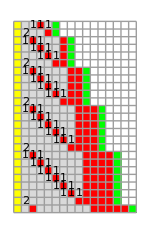


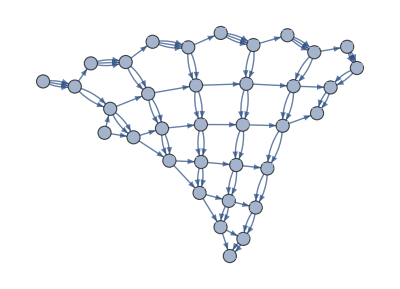
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "CAABAD",75,SSSMax->25, NetMax->35,SSSSize->150,NetSize->400, VertexSize->0.6];
```

```mathematica
sss90["RuleSet"]
```

{ABA→AAB,A→ABA}

```mathematica
sss90["Evolution"]
```

{CAABAD,CAAABD,CABAAABD,CAABAABD,CAAABABD,CAAAABBD,CABAAAABBD,CAABAAABBD,CAAABAABBD,CAAAABABBD,CAAAAABBBD,CABAAAAABBBD,CAABAAAABBBD,CAAABAAABBBD,CAAAABAABBBD,CAAAAABABBBD,CAAAAAABBBBD,CABAAAAAABBBBD,CAABAAAAABBBBD,CAAABAAAABBBBD,CAAAABAAABBBBD,CAAAAABAABBBBD,CAAAAAABABBBBD,CAAAAAAABBBBBD,CABAAAAAAABBBBBD,CAABAAAAAABBBBBD,CAAABAAAAABBBBBD,CAAAABAAAABBBBBD,CAAAAABAAABBBBBD,CAAAAAABAABBBBBD,CAAAAAAABABBBBBD,CAAAAAAAABBBBBBD,CABAAAAAAAABBBBBBD,CAABAAAAAAABBBBBBD,CAAABAAAAAABBBBBBD,CAAAABAAAAABBBBBBD,CAAAAABAAAABBBBBBD,CAAAAAABAAABBBBBBD,CAAAAAAABAABBBBBBD,CAAAAAAAABABBBBBBD,CAAAAAAAAABBBBBBBD,CABAAAAAAAAABBBBBBBD,CAABAAAAAAAABBBBBBBD,CAAABAAAAAAABBBBBBBD,CAAAABAAAAAABBBBBBBD,CAAAAABAAAAABBBBBBBD,CAAAAAABAAAABBBBBBBD,CAAAAAAABAAABBBBBBBD,CAAAAAAAABAABBBBBBBD,CAAAAAAAAABABBBBBBBD,CAAAAAAAAAABBBBBBBBD,CABAAAAAAAAAABBBBBBBBD,CAABAAAAAAAAABBBBBBBBD,CAAABAAAAAAAABBBBBBBBD,CAAAABAAAAAAABBBBBBBBD,CAAAAABAAAAAABBBBBBBBD,CAAAAAABAAAAABBBBBBBBD,CAAAAAAABAAAABBBBBBBBD,CAAAAAAAABAAABBBBBBBBD,CAAAAAAAAABAABBBBBBBBD,CAAAAAAAAAABABBBBBBBBD,CAAAAAAAAAAABBBBBBBBBD,CABAAAAAAAAAAABBBBBBBBBD,CAABAAAAAAAAAABBBBBBBBBD,CAAABAAAAAAAAABBBBBBBBBD,CAAAABAAAAAAAABBBBBBBBBD,CAAAAABAAAAAAABBBBBBBBBD,CAAAAAABAAAAAABBBBBBBBBD,CAAAAAAABAAAAABBBBBBBBBD,CAAAAAAAABAAAABBBBBBBBBD,CAAAAAAAAABAAABBBBBBBBBD,CAAAAAAAAAABAABBBBBBBBBD,CAAAAAAAAAAABABBBBBBBBBD,CAAAAAAAAAAAABBBBBBBBBBD,CABAAAAAAAAAAAABBBBBBBBBBD,CAABAAAAAAAAAAABBBBBBBBBBD}

```mathematica
sss90["Net"]
```

{2→3,2→3,2→3,3→4,3→4,1→4,4→5,4→5,1→5,3→6,6→7,6→7,6→7,7→8,7→8,4→8,8→9,8→9,5→9,9→10,9→10,5→10,7→11,11→12,11→12,11→12,12→13,12→13,8→13,13→14,13→14,9→14,14→15,14→15,10→15,15→16,15→16,10→16,12→17,17→18,17→18,17→18,18→19,18→19,13→19,19→20,19→20,14→20,20→21,20→21,15→21,21→22,21→22,16→22,22→23,22→23,16→23,18→24,24→25,24→25,24→25,25→26,25→26,19→26,26→27,26→27,20→27,27→28,27→28,21→28,28→29,28→29,22→29,29→30,29→30,23→30,30→31,30→31,23→31,25→32,32→33,32→33,32→33,33→34,33→34,26→34,34→35,34→35,27→35,35→36,35→36,28→36,36→37,36→37,29→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,31→40,33→41,41→42,41→42,41→42,42→43,42→43,34→43,43→44,43→44,35→44,44→45,44→45,36→45,45→46,45→46,37→46,46→47,46→47,38→47,47→48,47→48,39→48,48→49,48→49,40→49,49→50,49→50,40→50,42→51,51→52,51→52,51→52,52→53,52→53,43→53,53→54,53→54,44→54,54→55,54→55,45→55,55→56,55→56,46→56,56→57,56→57,47→57,57→58,57→58,48→58,58→59,58→59,49→59,59→60,59→60,50→60,60→61,60→61,50→61,52→62,62→63,62→63,62→63,63→64,63→64,53→64,64→65,64→65,54→65,65→66,65→66,55→66,66→67,66→67,56→67,67→68,67→68,57→68,68→69,68→69,58→69,69→70,69→70,59→70,70→71,70→71,60→71,71→72,71→72,61→72,72→73,72→73,61→73,63→74,74→75,74→75,74→75}

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

```mathematica
MaxStateLengthPositions[sss90]
```

{3,7,12,18,25,33,42,52,63}

Visually, these are the positions in the sessie (colored) image where the state string got longer.

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2D,{1,0,7,1},3
4
1,3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Identified as (probably) 2-dimensional, pattern valid starting from position 3.  In the 0^th row, provided by MaxStateLengthPositions, we see rapid, increasing growth.  In the row of 1^st differences, growth is linear.  The 2^nd differences row is constant, and the 3^rd differences row would be all 0.  (This is reminiscent of taking derivatives of a quadratic (2^nd-degree) polynomial:  the first derivative is a linear function, the 2^nd is a constant, the 3^rd is zero.

In this case it would make sense to rerun SSS, starting with row 3, since apparently the pattern did not stabilize until then:

```mathematica
sss90["Evolution"]⟦3⟧
```

CABAAABD

Other points to discuss:

Is dropping the first 10% a good strategy?  Is there a better one?

Is demanding 5 reps a good strategy?  What if after 5 reps, the pattern changes?  (Unlikely, for this MaxStateLengthPositions.)

Is demanding that the same rules must be used in all meaningful intervals a good strategy?  (MergeIntervalsByRulesUsed)

#### LeastUsedRulePositions: positions where the least-used rule was used

```mathematica
LeastUsedRulePositions[sss90]
```

{2,6,11,17,24,32,41,51,62,74}

```mathematica
sss90["RulesUsed"]
```

{1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2D,{1,0,8,1},2
4
1,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Again, the 2nd differences row is constant, indicating 2-d behavior.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last node that is n steps from origin on the undirected graph of "Net".

```mathematica
CheckDimension@DistanceLastPositions[sss90]
```

{2D,{1,0,6,1},5
5
1,5 | 10 | 16 | 23 | 31 | 40 | 50 | 61
5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 |  | }

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization for the directed graph.)

```mathematica
CheckDimension@DistanceTally[sss90]
```

{2D,{1,3,6,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimate[sss90,VertexLabels->"VertexWeight",NetSize->400]
```

#### GuessDimension: tries all 4 approximative tests, with appropriate checks, changes "Verdict" if appropriate.

```mathematica
GuessDimension[sss90]
```

```mathematica
sss90["Verdict"]
```

#### Other examples:

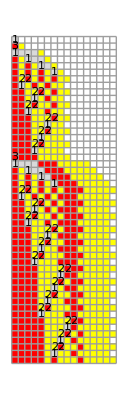
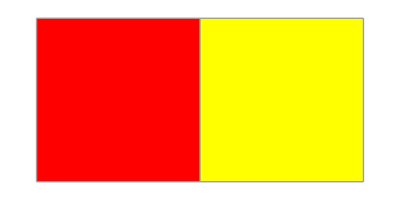
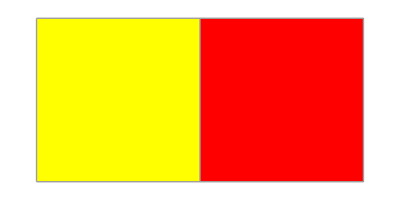

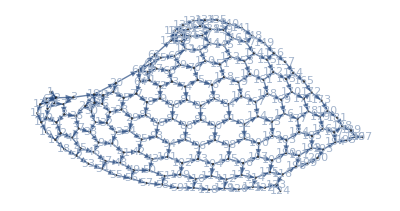
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssTemp=SSS[{"A"->"BC","CB"->"A","B"->"AAAA"},"A",700,SSSMax->50,NetMax->200];
```

```mathematica
sssTemp["RulesUsed"]
```

{1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,3,1,1,1,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

```mathematica
CheckDimension[LeastUsedRulePositions[sssTemp]]
```

{2D,{1,0,6,24},2
17
24,2 | 19 | 60 | 125 | 214 | 327 | 464 | 625
17 | 41 | 65 | 89 | 113 | 137 | 161 | 
24 | 24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[MaxStateLengthPositions[sssTemp]]
```

{2D,{1,0,5,24},7
17
24,7 | 24 | 65 | 130 | 219 | 332 | 469
17 | 41 | 65 | 89 | 113 | 137 | 
24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[DistanceLastPositions[sssTemp]]
```

{2D,{1,0,6,24},6
17
24,6 | 23 | 64 | 129 | 218 | 331 | 468 | 629
17 | 41 | 65 | 89 | 113 | 137 | 161 | 
24 | 24 | 24 | 24 | 24 | 24 |  | }

```mathematica
CheckDimension[DistanceTally[sssTemp]]
```

{2D,{2,0,14,3/2},1 | 2
1 | 4
3 | 0,1 | 2 | 6 | 10 | 17 | 24 | 34 | 44 | 57 | 70 | 86 | 102 | 121 | 140 | 162 | 184 | 209
1 | 4 | 4 | 7 | 7 | 10 | 10 | 13 | 13 | 16 | 16 | 19 | 19 | 22 | 22 | 25 | 
3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 | 0 | 3 |  | }

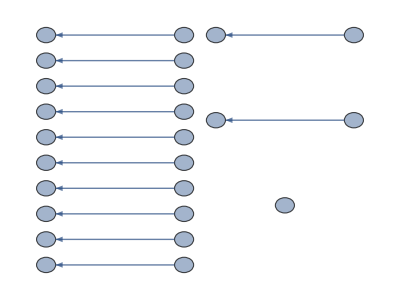
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Repeating

```mathematica
sss1a=SSS[{"A"->"",""->"A"},"",25,SSSSize->{50,200},NetSize->{400,300}, VertexSize->0.6];
sss1a["Verdict"]
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@MaxStateLengthPositions[sss1a]
```

{1D,{1,0,11,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

{failed,2
}

```mathematica
CheckDimension@DistanceTally[sss1a]
```

{failed,1
}

```mathematica
GuessDimension[sss1a]
```

Repeating

If the sessie is disconnected, neither DistanceTally nor DistanceLastPositions may generate a usable list.  But fortunately, any repeating sessie can automatically be assumed to have dimension 1.   This is supported by all tests for repeating, connected cases.  So GuessDimension returns immediately in these cases.

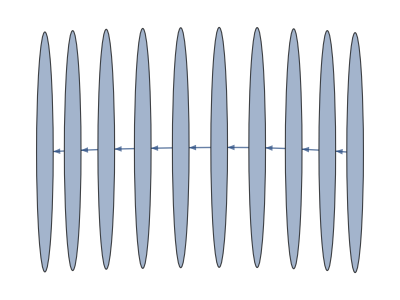
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Repeating

Repeating

{}

```mathematica
sss1b=SSS[4,20,SSSSize->{50,200},Max->10,NetSize->{400,300}, VertexSize->0.6];
sss1b["Verdict"]
GuessDimension[sss1b]
TestForUnusedRules[sss1b]
```

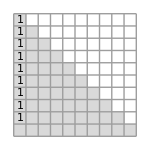
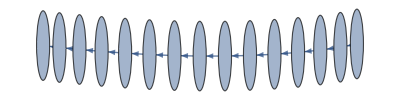
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

OK

1D

{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,19,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,18,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

1D

{}

```mathematica
sss20=SSS[20,20,SSSMax->10,SSSSize->{150,150},NetMax->15,NetSize->{400,100}, VertexSize->.8];
sss20["Verdict"]
GuessDimension[sss20]//Column
sss20["Verdict"]
TestForUnusedRules[sss20]
```

Note that GuessDimension has changed the "Verdict" field of sss20.

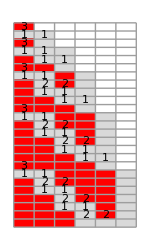


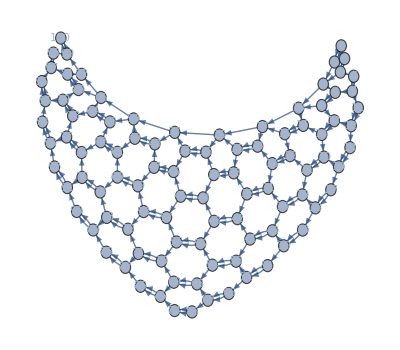
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

2D

{2D,{1,0,5,2},7
5
2,7 | 12 | 19 | 28 | 39 | 52 | 67
5 | 7 | 9 | 11 | 13 | 15 | 
2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},6
5
2,6 | 11 | 18 | 27 | 38 | 51 | 66 | 83
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{1,0,6,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | }
{2D,{3,0,6,4/3},1 | 2 | 4
1 | 2 | 3
1 | 1 | 2,1 | 2 | 4 | 7 | 12 | 18 | 25 | 34 | 44 | 55
1 | 2 | 3 | 5 | 6 | 7 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 |  | }

2D

```mathematica
sssHex=SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->25,SSSSize->{150,250},NetMax->100,NetSize->{400,350}, VertexSize->1];
sssHex["Verdict"]
GuessDimension[sssHex]//Column
sssHex["Verdict"]
```

```mathematica
TestForUnusedRules[sssHex]
```

{}

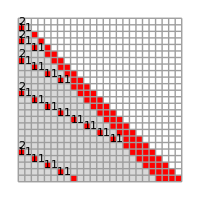
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

exp

{exp,{1,0,4,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 263
3 | 5 | 9 | 17 | 33 | 65 | 128 | 
2 | 4 | 8 | 16 | 32 | 63 |  | }
{exp,{1,0,6,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | }
{exp,{1,0,4,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | }
{exp,{2,0,4,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89
1 | 2 | 3 | 6 | 11 | 22 | 43 | 
1 | 1 | 3 | 5 | 11 | 21 |  | }

exp

```mathematica
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",264,SSSMax->25,SSSSize->{200,200},NetSize->{400,300}, VertexLabels->None];
GuessDimension[sssE]//Column
sssE["Verdict"]
```

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions.

```mathematica
Length[sssE["Evolution"]]
```

265

CheckDimension identifies the network as exponential soon as the sequence of ratios appears.  FixedPointList would continue until lines have zero length:

```mathematica
FixedPointList[Differences,MaxStateLengthPositions[sssE]]//Column
```

{3,6,11,20,37,70,135,263}
{3,5,9,17,33,65,128}
{2,4,8,16,32,63}
{2,4,8,16,31}
{2,4,8,15}
{2,4,7}
{2,3}
{1}
{}
{}

Interestingly, here the exponential behavior was only found in the DistanceTally data when running averages of pairs of integers were summed, the raw data is harder to recognize:

```mathematica
FixedPointList[Differences,DistanceTally[sssE]]//Column
```

{1,2,4,7,13,24,46,89}
{1,2,3,6,11,22,43}
{1,1,3,5,11,21}
{0,2,2,6,10}
{2,0,4,4}
{-2,4,0}
{6,-4}
{-10}
{}
{}

```mathematica
MovingAverage[#,2]& /@ FixedPointList[Differences,DistanceTally[sssE]][[;;-4]]//Column
```

{3/2,3,11/2,10,37/2,35,135/2}
{3/2,5/2,9/2,17/2,33/2,65/2}
{1,2,4,8,16}
{1,2,4,8}
{1,2,4}
{1,2}
{1}

# HSC Research Lunch Presentation

## Colton Davis and Ken Caviness

## Summarizing Networks

## “Sessie” (Sequential Substitution System)

## 1-d examples

### a)-Graphics- 𝕊_(n=1)^∞[{1}] =S[{1},{n,1,∞}]

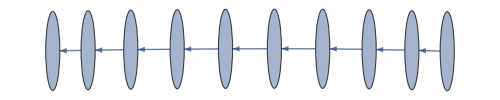
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
sss1a=SSS[{"A"->"A"},"A",50,Max->10,SSSSize->{20,200},NetSize->500];
```

Clues :
	MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,49,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
CheckDimension@DistanceTally[sss1a]
```

{1D,{1,0,48,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

{1D,{1,0,48,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
sss1a["Net"]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→26,26→27,27→28,28→29,29→30,30→31,31→32,32→33,33→34,34→35,35→36,36→37,37→38,38→39,39→40,40→41,41→42,42→43,43→44,44→45,45→46,46→47,47→48,48→49,49→50}

```mathematica
ToNetDifferenceSets[sss1a["Net"]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

𝕊_(n=1)^∞[{1}]

### b)-Graphics- 𝕊_(n=1)^∞[{1,1,2},{1},{1},{4}]

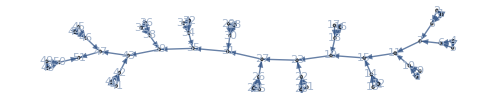
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss1b=SSS[{"AA"->"A",""->"AAA"},"",51,SSSMax->15,SSSSize->40,NetSize->500];
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1b]
```

{1D,{1,1,11,4},4
4,1 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | }

```mathematica
CheckDimension@DistanceTally[sss1b]
```

{1D,{1,3,10,4},6
4,1 | 3 | 4 | 6 | 10 | 14 | 18 | 22 | 26 | 30 | 34 | 38 | 42 | 46
2 | 1 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1b]
```

{1D,{1,0,12,4},3
4,3 | 7 | 11 | 15 | 19 | 23 | 27 | 31 | 35 | 39 | 43 | 47 | 51
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | }

```mathematica
sss1b["Net"]
```

{1→2,1→2,2→3,1→3,4→5,4→5,5→6,4→6,6→7,3→7,8→9,8→9,9→10,8→10,10→11,7→11,12→13,12→13,13→14,12→14,14→15,11→15,16→17,16→17,17→18,16→18,18→19,15→19,20→21,20→21,21→22,20→22,22→23,19→23,24→25,24→25,25→26,24→26,26→27,23→27,28→29,28→29,29→30,28→30,30→31,27→31,32→33,32→33,33→34,32→34,34→35,31→35,36→37,36→37,37→38,36→38,38→39,35→39,40→41,40→41,41→42,40→42,42→43,39→43,44→45,44→45,45→46,44→46,46→47,43→47,48→49,48→49,49→50,48→50,50→51,47→51}

```mathematica
ToNetDifferenceSets[sss1b["Net"]]
```

{{1,1,2},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1},{4},{1,1,2},{1},{1}}

𝕊_(n=1)^∞[{1,1,2},{1},{1},{4}]   or   𝕊_(n=1)^∞[{4},{1,1,2},{1},{1}]  or  ...

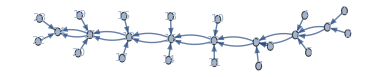
### c)-Graphics-

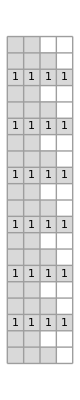
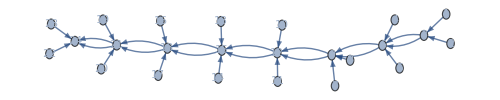
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss1c=SSS[{"AAAA"->"AA",""->"A"},"AA",24,SSSMax->20,ImageSize->100,NetSize->500];
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1c]
```

{1D,{1,0,7,3},3
3,3 | 6 | 9 | 12 | 15 | 18 | 21 | 24
3 | 3 | 3 | 3 | 3 | 3 | 3 | }

```mathematica
CheckDimension@DistanceTally[sss1c]
```

{1D,{1,1,6,3},3
3,1 | 3 | 6 | 9 | 12 | 15 | 18 | 21 | 23
2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1c]
```

{1D,{1,0,7,3},2
3,2 | 5 | 8 | 11 | 14 | 17 | 20 | 23
3 | 3 | 3 | 3 | 3 | 3 | 3 | }

```mathematica
sss1c["Net"]
```

{2→3,1→3,5→6,4→6,3→6,3→6,8→9,7→9,6→9,6→9,11→12,10→12,9→12,9→12,14→15,13→15,12→15,12→15,17→18,16→18,15→18,15→18,20→21,19→21,18→21,18→21,23→24,22→24,21→24,21→24}

```mathematica
ToNetDifferenceSets[sss1c["Net"]]
```

{{2},{1},{3,3},{2},{1},{3,3},{2},{1},{3,3},{2},{1},{3,3},{2},{1},{3,3},{2},{1},{3,3},{2},{1},{3,3},{2},{1}}

𝕊_(n=1)^∞[ {2},{1},{3,3}]

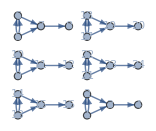
### d) -Graphics-

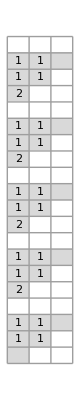
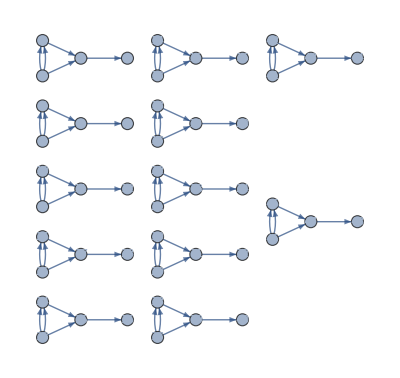
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss1d=SSS[{"AA"->"A","A"->"",""->"AAA"},"",48,SSSMax->20,ImageSize->100,NetSize->400];
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1d]
```

{1D,{1,0,11,4},4
4,4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | }

```mathematica
sss1d["Net"]
```

{1→2,1→2,2→3,1→3,3→4,5→6,5→6,6→7,5→7,7→8,9→10,9→10,10→11,9→11,11→12,13→14,13→14,14→15,13→15,15→16,17→18,17→18,18→19,17→19,19→20,21→22,21→22,22→23,21→23,23→24,25→26,25→26,26→27,25→27,27→28,29→30,29→30,30→31,29→31,31→32,33→34,33→34,34→35,33→35,35→36,37→38,37→38,38→39,37→39,39→40,41→42,41→42,42→43,41→43,43→44,45→46,45→46,46→47,45→47,47→48}

```mathematica
ToNetDifferenceSets[sss1d["Net"]]
```

{{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1},{},{1,1,2},{1},{1}}

𝕊_(n=1)^∞[ _______________]

### e) ?

```mathematica
sss1e=SSS[{},"",48,SSSMax->20,ImageSize->100,NetSize->500];
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1e]
```

{1D,{2,0,17,5/2},3 | 6
3 | 2,3 | 6 | 8 | 11 | 13 | 16 | 18 | 21 | 23 | 26 | 28 | 31 | 33 | 36 | 38 | 41 | 43 | 46 | 48
3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | 3 | 2 | }

```mathematica
CheckDimension@DistanceTally[sss1e]
```

{1D,{1,3,7,5},7
5,1 | 2 | 4 | 7 | 12 | 17 | 22 | 27 | 32 | 37 | 42
1 | 2 | 3 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1e]
```

{1D,{1,1,8,5},8
5,2 | 8 | 13 | 18 | 23 | 28 | 33 | 38 | 43 | 48
6 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | }

```mathematica
sss1e["Net"]
```

{2→3,2→3,1→3,1→3,5→6,5→6,4→6,4→6,7→8,7→8,6→8,3→8,10→11,10→11,9→11,9→11,12→13,12→13,11→13,8→13,15→16,15→16,14→16,14→16,17→18,17→18,16→18,13→18,20→21,20→21,19→21,19→21,22→23,22→23,21→23,18→23,25→26,25→26,24→26,24→26,27→28,27→28,26→28,23→28,30→31,30→31,29→31,29→31,32→33,32→33,31→33,28→33,35→36,35→36,34→36,34→36,37→38,37→38,36→38,33→38,40→41,40→41,39→41,39→41,42→43,42→43,41→43,38→43,45→46,45→46,44→46,44→46,47→48,47→48,46→48,43→48}

```mathematica
ToNetDifferenceSets[sss1e["Net"]]
```

{{2,2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1},{5},{2,2},{1,1},{2},{1,1}}

𝕊_(n=1)^∞[ _______________]

## 2-d

#### a) connects to neighbors (East and North): 𝕊_(n=1)^∞[n·{n,n+1}]

-Graphics-

Note the “clue” integers, taken from the left side or the bottom sides!

```mathematica
CheckDimension[{1,2,4,7,11,16,22}]
```

{2D,{1,0,5,1},1
1
1,1 | 2 | 4 | 7 | 11 | 16 | 22
1 | 2 | 3 | 4 | 5 | 6 | 
1 | 1 | 1 | 1 | 1 |  | }

```mathematica
CheckDimension[{1,3,6,10,15,21,28}]
```

{2D,{1,0,5,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28
2 | 3 | 4 | 5 | 6 | 7 | 
1 | 1 | 1 | 1 | 1 |  | }

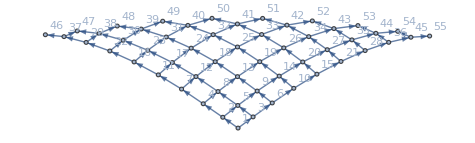

```mathematica
net2dN={1->2,1->3,2->4,2->5,4->7,4->8,7->11,7->12,11->16,11->17,16->22,16->23,22->29,22->30,29->37,29->38,37->46,37->47,3->5,3->6,5->8,5->9,8->12,8->13,12->17,12->18,17->23,17->24,23->30,23->31,30->38,30->39,38->47,38->48,6->9,6->10,9->13,9->14,13->18,13->19,18->24,18->25,24->31,24->32,31->39,31->40,39->48,39->49,10->14,10->15,14->19,14->20,19->25,19->26,25->32,25->33,32->40,32->41,40->49,40->50,15->20,15->21,20->26,20->27,26->33,26->34,33->41,33->42,41->50,41->51,21->27,21->28,27->34,27->35,34->42,34->43,42->51,42->52,28->35,28->36,35->43,35->44,43->52,43->53,36->44,36->45,44->53,44->54,45->54,45->55};
```

```mathematica
ToNetDifferenceSets[net2dN]
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

```mathematica
ToReducedNetDifferenceSets[%]
```

{{1,2},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}}}

“Shift & Subtract”:

2·{{2,3}}, | 3·{{3,4}}, | 4·{{4,5}}, | 5·{{5,6}}, | 6·{{6,7}}, | …
1·{{1,2}}, | 2·{{2,3}}, | 3·{{3,4}}, | 4·{{4,5}}, | 5·{{5,6}}, | …
1·{{1,1}}, | 1·{{1,1}}, | 1·{{1,1}}, | 1·{{1,1}}, | 1·{{1,1}}, | …

𝕊_(n=1)^∞[n·{n,n+1}]

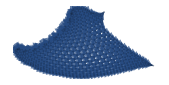
#### b) first "hex" network: -Graphics-

```mathematica
sss2b=SSS[{"A"->"BC","CB"->"A","B"->"AAAA"},"A",700,SSSMax->50,NetMax->200];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
Sort@sss2b["Net"]
```

{1→2,2→3,2→4,2→5,2→6,3→7,3→19,4→7,4→9,5→9,5→13,6→13,7→8,8→11,8→36,9→10,10→11,10→15,11→12,12→17,12→44,13→14,14→15,15→16,16→17,17→18,18→52,19→20,19→21,19→22,19→23,20→24,20→60,21→24,21→26,22→26,22→30,23→30,23→36,24→25,25→28,25→77,26→27,27→28,27→32,28→29,29→34,29→85,30→31,31→32,31→38,32→33,33→34,33→40,34→35,35→42,35→93,36→37,37→38,37→44,38→39,39→40,39→46,40→41,41→42,41→48,42→43,43→50,43→101,44→45,45→46,45→52,46→47,47→48,47→54,48→49,49→50,49→56,50→51,51→58,51→109,52→53,53→54,54→55,55→56,56→57,57→58,58→59,59→117,60→61,60→62,60→63,60→64,61→65,61→125,62→65,62→67,63→67,63→71,64→71,64→77,65→66,66→69,66→142,67→68,68→69,68→73,69→70,70→75,70→150,71→72,72→73,72→79,73→74,74→75,74→81,75→76,76→83,76→158,77→78,78→79,78→85,79→80,80→81,80→87,81→82,82→83,82→89,83→84,84→91,84→166,85→86,86→87,86→93,87→88,88→89,88→95,89→90,90→91,90→97,91→92,92→99,92→174,93→94,94→95,94→101,95→96,96→97,96→103,97→98,98→99,98→105,99→100,100→107,100→182,101→102,102→103,102→109,103→104,104→105,104→111,105→106,106→107,106→113,107→108,108→115,108→190,109→110,110→111,110→117,111→112,112→113,112→119,113→114,114→115,114→121,115→116,116→123,116→198,117→118,118→119,119→120,120→121,121→122,122→123,123→124,124→206,125→126,125→127,125→128,125→129,126→130,126→214,127→130,127→132,128→132,128→136,129→136,129→142,130→131,131→134,131→231,132→133,133→134,133→138,134→135,135→140,135→239,136→137,137→138,137→144,138→139,139→140,139→146,140→141,141→148,141→247,142→143,143→144,143→150,144→145,145→146,145→152,146→147,147→148,147→154,148→149,149→156,149→255,150→151,151→152,151→158,152→153,153→154,153→160,154→155,155→156,155→162,156→157,157→164,157→263,158→159,159→160,159→166,160→161,161→162,161→168,162→163,163→164,163→170,164→165,165→172,165→271,166→167,167→168,167→174,168→169,169→170,169→176,170→171,171→172,171→178,172→173,173→180,173→279,174→175,175→176,175→182,176→177,177→178,177→184,178→179,179→180,179→186,180→181,181→188,181→287,182→183,183→184,183→190,184→185,185→186,185→192,186→187,187→188,187→194,188→189,189→196,189→295,190→191,191→192,191→198,192→193,193→194,193→200,194→195,195→196,195→202,196→197,197→204,197→303,198→199,199→200,199→206,200→201,201→202,201→208,202→203,203→204,203→210,204→205,205→212,205→311,206→207,207→208,208→209,209→210,210→211,211→212,212→213,213→319,214→215,214→216,214→217,214→218,215→219,215→327,216→219,216→221,217→221,217→225,218→225,218→231,219→220,220→223,220→344,221→222,222→223,222→227,223→224,224→229,224→352,225→226,226→227,226→233,227→228,228→229,228→235,229→230,230→237,230→360,231→232,232→233,232→239,233→234,234→235,234→241,235→236,236→237,236→243,237→238,238→245,238→368,239→240,240→241,240→247,241→242,242→243,242→249,243→244,244→245,244→251,245→246,246→253,246→376,247→248,248→249,248→255,249→250,250→251,250→257,251→252,252→253,252→259,253→254,254→261,254→384,255→256,256→257,256→263,257→258,258→259,258→265,259→260,260→261,260→267,261→262,262→269,262→392,263→264,264→265,264→271,265→266,266→267,266→273,267→268,268→269,268→275,269→270,270→277,270→400,271→272,272→273,272→279,273→274,274→275,274→281,275→276,276→277,276→283,277→278,278→285,278→408,279→280,280→281,280→287,281→282,282→283,282→289,283→284,284→285,284→291,285→286,286→293,286→416,287→288,288→289,288→295,289→290,290→291,290→297,291→292,292→293,292→299,293→294,294→301,294→424,295→296,296→297,296→303,297→298,298→299,298→305,299→300,300→301,300→307,301→302,302→309,302→432,303→304,304→305,304→311,305→306,306→307,306→313,307→308,308→309,308→315,309→310,310→317,310→440,311→312,312→313,312→319,313→314,314→315,314→321,315→316,316→317,316→323,317→318,318→325,318→448,319→320,320→321,321→322,322→323,323→324,324→325,325→326,326→456,327→328,327→329,327→330,327→331,328→332,328→464,329→332,329→334,330→334,330→338,331→338,331→344,332→333,333→336,333→481,334→335,335→336,335→340,336→337,337→342,337→489,338→339,339→340,339→346,340→341,341→342,341→348,342→343,343→350,343→497,344→345,345→346,345→352,346→347,347→348,347→354,348→349,349→350,349→356,350→351,351→358,351→505,352→353,353→354,353→360,354→355,355→356,355→362,356→357,357→358,357→364,358→359,359→366,359→513,360→361,361→362,361→368,362→363,363→364,363→370,364→365,365→366,365→372,366→367,367→374,367→521,368→369,369→370,369→376,370→371,371→372,371→378,372→373,373→374,373→380,374→375,375→382,375→529,376→377,377→378,377→384,378→379,379→380,379→386,380→381,381→382,381→388,382→383,383→390,383→537,384→385,385→386,385→392,386→387,387→388,387→394,388→389,389→390,389→396,390→391,391→398,391→545,392→393,393→394,393→400,394→395,395→396,395→402,396→397,397→398,397→404,398→399,399→406,399→553,400→401,401→402,401→408,402→403,403→404,403→410,404→405,405→406,405→412,406→407,407→414,407→561,408→409,409→410,409→416,410→411,411→412,411→418,412→413,413→414,413→420,414→415,415→422,415→569,416→417,417→418,417→424,418→419,419→420,419→426,420→421,421→422,421→428,422→423,423→430,423→577,424→425,425→426,425→432,426→427,427→428,427→434,428→429,429→430,429→436,430→431,431→438,431→585,432→433,433→434,433→440,434→435,435→436,435→442,436→437,437→438,437→444,438→439,439→446,439→593,440→441,441→442,441→448,442→443,443→444,443→450,444→445,445→446,445→452,446→447,447→454,447→601,448→449,449→450,449→456,450→451,451→452,451→458,452→453,453→454,453→460,454→455,455→462,455→609,456→457,457→458,458→459,459→460,460→461,461→462,462→463,463→617,464→465,464→466,464→467,464→468,465→469,465→625,466→469,466→471,467→471,467→475,468→475,468→481,469→470,470→473,470→642,471→472,472→473,472→477,473→474,474→479,474→650,475→476,476→477,476→483,477→478,478→479,478→485,479→480,480→487,480→658,481→482,482→483,482→489,483→484,484→485,484→491,485→486,486→487,486→493,487→488,488→495,488→666,489→490,490→491,490→497,491→492,492→493,492→499,493→494,494→495,494→501,495→496,496→503,496→674,497→498,498→499,498→505,499→500,500→501,500→507,501→502,502→503,502→509,503→504,504→511,504→682,505→506,506→507,506→513,507→508,508→509,508→515,509→510,510→511,510→517,511→512,512→519,512→690,513→514,514→515,514→521,515→516,516→517,516→523,517→518,518→519,518→525,519→520,520→527,520→698,521→522,522→523,522→529,523→524,524→525,524→531,525→526,526→527,526→533,527→528,528→535,529→530,530→531,530→537,531→532,532→533,532→539,533→534,534→535,534→541,535→536,536→543,537→538,538→539,538→545,539→540,540→541,540→547,541→542,542→543,542→549,543→544,544→551,545→546,546→547,546→553,547→548,548→549,548→555,549→550,550→551,550→557,551→552,552→559,553→554,554→555,554→561,555→556,556→557,556→563,557→558,558→559,558→565,559→560,560→567,561→562,562→563,562→569,563→564,564→565,564→571,565→566,566→567,566→573,567→568,568→575,569→570,570→571,570→577,571→572,572→573,572→579,573→574,574→575,574→581,575→576,576→583,577→578,578→579,578→585,579→580,580→581,580→587,581→582,582→583,582→589,583→584,584→591,585→586,586→587,586→593,587→588,588→589,588→595,589→590,590→591,590→597,591→592,592→599,593→594,594→595,594→601,595→596,596→597,596→603,597→598,598→599,598→605,599→600,600→607,601→602,602→603,602→609,603→604,604→605,604→611,605→606,606→607,606→613,607→608,608→615,609→610,610→611,610→617,611→612,612→613,612→619,613→614,614→615,614→621,615→616,616→623,617→618,618→619,619→620,620→621,621→622,622→623,623→624,625→626,625→627,625→628,625→629,626→630,627→630,627→632,628→632,628→636,629→636,629→642,630→631,631→634,632→633,633→634,633→638,634→635,635→640,636→637,637→638,637→644,638→639,639→640,639→646,640→641,641→648,642→643,643→644,643→650,644→645,645→646,645→652,646→647,647→648,647→654,648→649,649→656,650→651,651→652,651→658,652→653,653→654,653→660,654→655,655→656,655→662,656→657,657→664,658→659,659→660,659→666,660→661,661→662,661→668,662→663,663→664,663→670,664→665,665→672,666→667,667→668,667→674,668→669,669→670,669→676,670→671,671→672,671→678,672→673,673→680,674→675,675→676,675→682,676→677,677→678,677→684,678→679,679→680,679→686,680→681,681→688,682→683,683→684,683→690,684→685,685→686,685→692,686→687,687→688,687→694,688→689,689→696,690→691,691→692,691→698,692→693,693→694,693→700,694→695,695→696,696→697,698→699,699→700}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss2b["Net"]]
```

```mathematica
{{1},
{1,2,3,4},{4,16},{3,5},{4,8},{7},{1},{3,28},{1},{1,5},{1},{5,32},5·{{1}},{34},{1,2,3,4},{4,40},{3,5},{4,8},{7,13},{1},{3,52},{1},{1,5},{1},{5,56},2·{{1},{1,7}},{1},{7,58},3·{{1},{1,7}},{1},{7,58},3·{{1},{1,7}},{1},{7,58},7·{{1}},{58},
{1,2,3,4},{4,64},{3,5},{4,8},{7,13},{1},{3,76},{1},{1,5},{1},{5,80},2·{{1},{1,7}},{1},{7,82},3·{{1},{1,7}},{1},{7,82},3·{{1},{1,7}},{1},{7,82},3·{{1},{1,7}},{1},{7,82},3·{{1},{1,7}},{1},{7,82},3·{{1},{1,7}},{1},{7,82},7·{{1}},{82},{1,2,3,4},{4,88},{3,5},{4,8},{7,13},{1},{3,100},{1},{1,5},{1},{5,104},2·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},3·{{1},{1,7}},{1},{7,106},7·{{1}},{106},{1,2,3,4},{4,112},{3,5},{4,8},{7,13},{1},{3,124},{1},{1,5},{1},{5,128},2·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},3·{{1},{1,7}},{1},{7,130},7·{{1}},{130},{1,2,3,4},{4,136},{3,5},{4,8},{7,13},{1},{3,148},{1},{1,5},{1},{5,152},2·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},3·{{1},{1,7}},{1},{7,154},7·{{1}},{154},{1,2,3,4},{4,160},{3,5},{4,8},{7,13},{1},{3,172},{1},{1,5},{1},{5,176},2·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7,178},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},7·{{1}},{},{1,2,3,4},{4},{3,5},{4,8},{7,13},{1},{3},{1},{1,5},{1},{5},2·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},3·{{1},{1,7}},{1},{7},2·{{1},{1,7}},3·{{1}},{},2·{{1}}}
```

𝕊_(n=1)^∞[   ]

#### c)-Graphics- 𝕊_(n=2)^∞[{i,j},(i-1)·{{1,1},{1,i,j}},{i,j,k},{1,2},{j,k},i·{{1,1},{1,j,k}},{k,l},{1,2}]

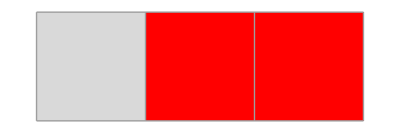
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2c=SSS[{"AA"->"AB","ABB"->"ABA","B"->"AA"},"B",300,SSSMax->20,SSSSize->100,NetSize->450,VertexLabels->None];
```

```mathematica
GuessDimension[sss2c]
```

2D

{{2D,{1,0,18,1},9
4
1,9 | 13 | 18 | 24 | 31 | 39 | 48 | 58 | 69 | 81 | 94 | 108 | 123 | 139 | 156 | 174 | 193 | 213 | 234 | 256
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,19,1},8
4
1,8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 107 | 122 | 138 | 155 | 173 | 192 | 212 | 233 | 255 | 278
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,18,1},11
5
1,11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191 | 211 | 232 | 254 | 277
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,22,1},1
1
1,1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191 | 211 | 232 | 254 | 277
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
ToNetDifferenceSets@sss2c["Net"]
```

{{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{3,4},{1,1},{3,4,5},{1,2},{4,5},{1,1},{1,4,5},{5,6},{1,2},{5,6},{1,1},{1,5,6},{1,1},{5,6,7},{1,2},{6,7},{1,1},{1,6,7},{1,1},{1,6,7},{7,8},{1,2},{7,8},{1,1},{1,7,8},{1,1},{1,7,8},{1,1},{7,8,9},{1,2},{8,9},{1,1},{1,8,9},{1,1},{1,8,9},{1,1},{1,8,9},{9,10},{1,2},{9,10},{1,1},{1,9,10},{1,1},{1,9,10},{1,1},{1,9,10},{1,1},{9,10,11},{1,2},{10,11},{1,1},{1,10,11},{1,1},{1,10,11},{1,1},{1,10,11},{1,1},{1,10,11},{11,12},{1,2},{11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{1,11,12},{1,1},{11,12,13},{1,2},{12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{1,1},{1,12,13},{13,14},{1,2},{13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{1,13,14},{1,1},{13,14,15},{1,2},{14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{1,1},{1,14,15},{15,16},{1,2},{15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{1,15,16},{1,1},{15,16,17},{1,2},{16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{1,1},{1,16,17},{17,18},{1,2},{17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{1,17,18},{1,1},{17,18,19},{1,2},{18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{1,1},{1,18,19},{19,20},{1,2},{19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{1,19,20},{1,1},{19,20,21},{1,2},{20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{1,1},{1,20,21},{21,22},{1,2},{21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{1,21,22},{1,1},{21,22,23},{1,2},{22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{1,1},{1,22,23},{23},{1,2},{},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1}}

```mathematica
ToReducedNetDifferenceSets[%]
```

{{1,1},{1,2},{1,4},2·{{1,2}},{2,3},{3,4},{1,2},{3,4},{1,1},{3,4,5},{1,2},{4,5},{1,1},{1,4,5},{5,6},{1,2},{5,6},{1,1},{1,5,6},{1,1},{5,6,7},{1,2},{6,7},2·{{1,1},{1,6,7}},{7,8},{1,2},{7,8},2·{{1,1},{1,7,8}},{1,1},{7,8,9},{1,2},{8,9},3·{{1,1},{1,8,9}},{9,10},{1,2},{9,10},3·{{1,1},{1,9,10}},{1,1},{9,10,11},{1,2},{10,11},4·{{1,1},{1,10,11}},{11,12},{1,2},{11,12},4·{{1,1},{1,11,12}},{1,1},{11,12,13},{1,2},{12,13},5·{{1,1},{1,12,13}},{13,14},{1,2},{13,14},5·{{1,1},{1,13,14}},{1,1},{13,14,15},{1,2},{14,15},6·{{1,1},{1,14,15}},{15,16},{1,2},{15,16},6·{{1,1},{1,15,16}},{1,1},{15,16,17},{1,2},{16,17},7·{{1,1},{1,16,17}},{17,18},{1,2},{17,18},7·{{1,1},{1,17,18}},{1,1},{17,18,19},{1,2},{18,19},8·{{1,1},{1,18,19}},{19,20},{1,2},{19,20},8·{{1,1},{1,19,20}},{1,1},{19,20,21},{1,2},{20,21},9·{{1,1},{1,20,21}},{21,22},{1,2},{21,22},9·{{1,1},{1,21,22}},{1,1},{21,22,23},{1,2},{22,23},10·{{1,1},{1,22,23}},{23},{1,2},{},10·{{1,1},{1}}}

𝕊_(n=2)^∞[{i,j},(i-1)·{{1,1},{1,i,j}},{i,j,k},{1,2},{j,k},i·{{1,1},{1,j,k}},{k,l},{1,2}]

i=2n-1, j=2n, k=2n+1, l=2n+2

#### d) ? 𝕊_(n=1)^∞[{1,1,2},{1,n+1},(n-1)·{{1,n+3}},{n+3}]

## 3-d

### a) connect to neighbors (E, N, Up)

-Graphics-

-Graphics-

{1·{{1,2,3}},1·{{3,4,5}},2·{{3,5,6}},1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}},1·{{36,37,38}},2·{{36,38,39}},3·{{36,39,40}},4·{{36,40,41}},5·{{36,41,42}},6·{{36,42,43}},7·{{36,43,44}},8·{{36,44,45}},1·{{45,46,47}},2·{{45,47,48}},3·{{45,48,49}},4·{{45,49,50}},5·{{45,50,51}},6·{{45,51,52}},7·{{45,52,53}},8·{{45,53,54}},9·{{45,54,55}},1·{{55,56,57}},2·{{55,57,58}},3·{{55,58,59}},4·{{55,59,60}},5·{{55,60,61}},6·{{55,61,62}},7·{{55,62,63}},8·{{55,63,64}},9·{{55,64,65}},10·{{55,65,66}},1·{{66,67,68}},2·{{66,68,69}},3·{{66,69,70}},4·{{66,70,71}},5·{{66,71,72}},6·{{66,72,73}},7·{{66,73,74}},8·{{66,74,75}},9·{{66,75,76}},10·{{66,76,77}},11·{{66,77,78}},1·{{78,79,80}},2·{{78,80,81}},3·{{78,81,82}},4·{{78,82,83}},5·{{78,83,84}},6·{{78,84,85}},7·{{78,85,86}},8·{{78,86,87}},9·{{78,87,88}},10·{{78,88,89}},11·{{78,89,90}},12·{{78,90,91}},1·{{91,92,93}},2·{{91,93,94}},3·{{91,94,95}},4·{{91,95,96}},5·{{91,96,97}},6·{{91,97,98}},7·{{91,98,99}},8·{{91,99,100}},9·{{91,100,101}},10·{{91,101,102}},11·{{91,102,103}},12·{{91,103,104}},13·{{91,104,105}}}

𝕊_(n=1)^∞𝕊_(i=1)^n[i·{a_n,a_n+i,a_n+i+1}], a_n=Δ_(n-1)=(n-1)n/2

𝕊_(n=1)^∞𝕊_(i=1)^n[i·{(n-1)n/2,(n-1)n/2+i,(n-1)n/2+i+1}]

## Simple constructed rulesets to generate N-d networks

### 1-d: a simple “band” structure network

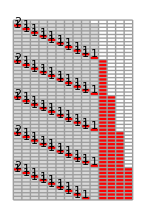
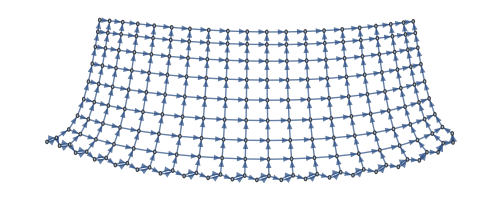
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss1X=SSS[{"BA"->"AB","A"->"BA"},"AAAAAAAAA",200,SSSMax->50,SSSSize->{100,150},NetSize->{500,200},VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
GuessDimension[sss1X]
```

1D

{{1D,{1,0,18,10},2
10,2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92 | 102 | 112 | 122 | 132 | 142 | 152 | 162 | 172 | 182
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{1D,{1,0,19,10},1
10,1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91 | 101 | 111 | 121 | 131 | 141 | 151 | 161 | 171 | 181 | 191
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{1D,{1,1,18,10},13
10,11 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93 | 103 | 113 | 123 | 133 | 143 | 153 | 163 | 173 | 183 | 193
2 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss1X["Net"][[;;100]]]
```

```mathematica
{{1,1},{1,9},7·{{1,10}},{10},{1,1},{1,9},7·{{1,10}},{10},{1,1},{1,9},7·{{1,10}},{10},{1,1},{1,9},7·{{1,10}},{10},{1,1},{1,9},5·{{1,10}},2·{{1}},{},{1,1},6·{{1}}}
```

𝕊_(n=1)^∞[{1,1},{1,9},7·{1,10},{10}]

### 2-d: small modification of previous 1-d case

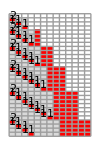
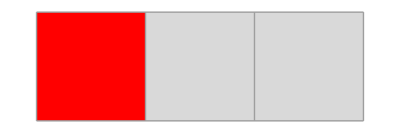
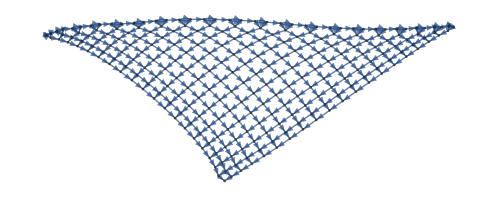
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2X=SSS[{"BA"->"AB","A"->"BAA"},"A",250,SSSMax->30,SSSSize->{100,150},NetSize->{500,200},VertexLabels->Placed["Name",Tooltip]];
```

```mathematica
GuessDimension[sss2X]
```

2D

{{2D,{1,0,17,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 | 90 | 104 | 119 | 135 | 152 | 170 | 189 | 209
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,18,1},1
3
1,1 | 4 | 8 | 13 | 19 | 26 | 34 | 43 | 53 | 64 | 76 | 89 | 103 | 118 | 134 | 151 | 169 | 188 | 208 | 229
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,17,1},3
4
1,3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63 | 75 | 88 | 102 | 117 | 133 | 150 | 168 | 187 | 207 | 228
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{2,0,17,1/2},1 | 3
2 | 2
0 | 1,1 | 3 | 5 | 8 | 11 | 15 | 19 | 24 | 29 | 35 | 41 | 48 | 55 | 63 | 71 | 80 | 89 | 99 | 109 | 120
2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss2X["Net"]
```

{{1,1,2},{1,2},{4},{1,1,2},{1,3},{1,5},{5},{1,1,2},{1,4},2·{{1,6}},{6},{1,1,2},{1,5},3·{{1,7}},{7},{1,1,2},{1,6},4·{{1,8}},{8},{1,1,2},{1,7},5·{{1,9}},{9},{1,1,2},{1,8},6·{{1,10}},{10},{1,1,2},{1,9},7·{{1,11}},{11},{1,1,2},{1,10},8·{{1,12}},{12},{1,1,2},{1,11},9·{{1,13}},{13},{1,1,2},{1,12},10·{{1,14}},{14},{1,1,2},{1,13},11·{{1,15}},{15},{1,1,2},{1,14},12·{{1,16}},{16},{1,1,2},{1,15},13·{{1,17}},{17},{1,1,2},{1,16},14·{{1,18}},{18},{1,1,2},{1,17},15·{{1,19}},{19},{1,1,2},{1,18},16·{{1,20}},{20},{1,1,2},{1,19},17·{{1,21}},{21},{1,1,2},{1,20},18·{{1,22}},{22},{1,1,2},20·{{1}}}

𝕊_(n=1)^∞[{1,1,2},{1,n+1},(n-1)·{1,n+3},{n+3}]

### “exponential”:

#### a) arbitrary example

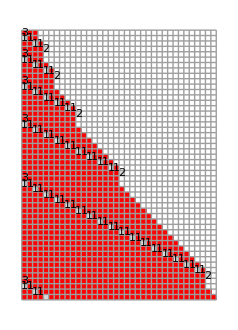
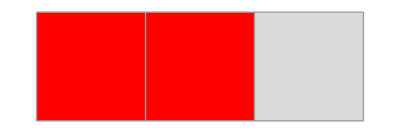
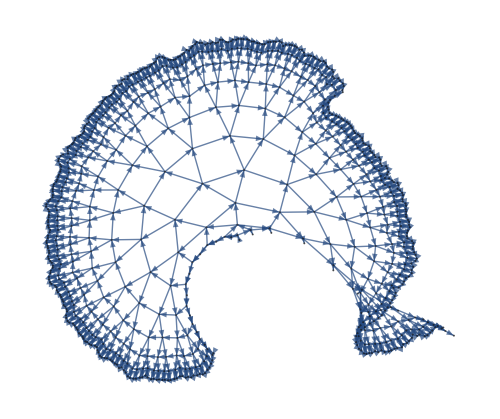
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssEXP1=SSS[{"AB"->"BBA","A"->"","B"->"A"},"BBB",800,SSSMax->50,SSSSize->100,NetSize->500,VertexLabels->None];
```

```mathematica
GuessDimension[sssEXP1]
```

exp

{{exp,{1,0,4,2},4
5
2,4 | 9 | 16 | 27 | 46 | 81 | 148
5 | 7 | 11 | 19 | 35 | 67 | 
2 | 4 | 8 | 16 | 32 |  | },{exp,{1,0,4,2},4
5
2,4 | 9 | 16 | 27 | 46 | 81 | 148
5 | 7 | 11 | 19 | 35 | 67 | 
2 | 4 | 8 | 16 | 32 |  | },{exp,{1,0,5,2},2
4
1,2 | 6 | 11 | 18 | 29 | 48 | 83 | 150
4 | 5 | 7 | 11 | 19 | 35 | 67 | 
1 | 2 | 4 | 8 | 16 | 32 |  | },{exp,{1,2,4,2},5
5
2,1 | 2 | 5 | 10 | 17 | 28 | 47 | 82 | 149
1 | 3 | 5 | 7 | 11 | 19 | 35 | 67 | 
2 | 2 | 2 | 4 | 8 | 16 | 32 |  | }}

```mathematica
ToNetDifferenceSets[sssEXP1["Net"]]
```

```mathematica
{{1},{1,3,4},{1,4,5},{},{1},{1,4,5},{1,5,6},{1,6,7},{},{1},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{1,10,11},{},{1},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{1,16,17},{1,17,18},{1,18,19},{},{1},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{1,32,33},{1,33,34},{1,34,35},{},{1},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{1,64,65},{1,65,66},{1,66,67},{},{1},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
```

𝕊_(n=1)^∞[{1},𝕊_(i=2^(n-1)+2,2^(n-1)+3,…)^(2^n+1)[{1,i,i+1}],{}]

#### b) small modification of previous constructed 2-d case

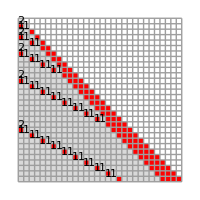
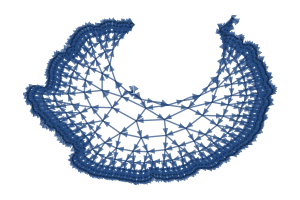
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssExpX=SSS[{"BA"->"AAB","A"->"BA"},"A",850,SSSMax->30,SSSSize->{200,200},NetSize->{300,200},RulePlacement->Left,
VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sssExpX]
```

exp

{{exp,{1,0,6,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{1,0,7,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{1,0,6,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134 | 263 | 520
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 |  | },{exp,{2,0,6,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89 | 175 | 346
1 | 2 | 3 | 6 | 11 | 22 | 43 | 86 | 171 | 
1 | 1 | 3 | 5 | 11 | 21 | 43 | 85 |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sssExpX["Net"]
```

```mathematica
{{1,1},{1,3},{1,1},{1,2,4},{4,5},{1,1},{1,4,6},{1,6,7},{1,7,8},{8,9},{1,1},{1,8,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{1,15,16},{16,17},{1,1},{1,16,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{1,31,32},{32,33},{1,1},{1,32,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{1,63,64},{64,65},{1,1},{1,64,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{1,127,128},{128,129},{1,1},{1,128,130},{1,130,131},{1,131,132},{1,132,133},{1,133,134},{1,134,135},{1,135,136},{1,136,137},{1,137,138},{1,138,139},{1,139,140},{1,140,141},{1,141,142},{1,142,143},{1,143,144},{1,144,145},{1,145,146},{1,146,147},{1,147,148},{1,148,149},{1,149,150},{1,150,151},{1,151,152},{1,152,153},{1,153,154},{1,154,155},{1,155,156},{1,156,157},{1,157,158},{1,158,159},{1,159,160},{1,160,161},{1,161,162},{1,162,163},{1,163,164},{1,164,165},{1,165,166},{1,166,167},{1,167,168},{1,168,169},{1,169,170},{1,170,171},{1,171,172},{1,172,173},{1,173,174},{1,174,175},{1,175,176},{1,176,177},{1,177,178},{1,178,179},{1,179,180},{1,180,181},{1,181,182},{1,182,183},{1,183,184},{1,184,185},{1,185,186},{1,186,187},{1,187,188},{1,188,189},{1,189,190},{1,190,191},{1,191,192},{1,192,193},{1,193,194},{1,194,195},{1,195,196},{1,196,197},{1,197,198},{1,198,199},{1,199,200},{1,200,201},{1,201,202},{1,202,203},{1,203,204},{1,204,205},{1,205,206},{1,206,207},{1,207,208},{1,208,209},{1,209,210},{1,210,211},{1,211,212},{1,212,213},{1,213,214},{1,214,215},{1,215,216},{1,216,217},{1,217,218},{1,218,219},{1,219,220},{1,220,221},{1,221,222},{1,222,223},{1,223,224},{1,224,225},{1,225,226},{1,226,227},{1,227,228},{1,228,229},{1,229,230},{1,230,231},{1,231,232},{1,232,233},{1,233,234},{1,234,235},{1,235,236},{1,236,237},{1,237,238},{1,238,239},{1,239,240},{1,240,241},{1,241,242},{1,242,243},{1,243,244},{1,244,245},{1,245,246},{1,246,247},{1,247,248},{1,248,249},{1,249,250},{1,250,251},{1,251,252},{1,252,253},{1,253,254},{1,254,255},{1,255,256},{256,257},{1,1},{1,256,258},{1,258,259},{1,259,260},{1,260,261},{1,261,262},{1,262,263},{1,263,264},{1,264,265},{1,265,266},{1,266,267},{1,267,268},{1,268,269},{1,269,270},{1,270,271},{1,271,272},{1,272,273},{1,273,274},{1,274,275},{1,275,276},{1,276,277},{1,277,278},{1,278,279},{1,279,280},{1,280,281},{1,281,282},{1,282,283},{1,283,284},{1,284,285},{1,285,286},{1,286,287},{1,287,288},{1,288,289},{1,289,290},{1,290,291},{1,291,292},{1,292,293},{1,293,294},{1,294,295},{1,295,296},{1,296,297},{1,297,298},{1,298,299},{1,299,300},{1,300,301},{1,301,302},{1,302,303},{1,303,304},{1,304,305},{1,305,306},{1,306,307},{1,307,308},{1,308,309},{1,309,310},{1,310,311},{1,311,312},{1,312,313},{1,313,314},{1,314,315},{1,315,316},{1,316,317},{1,317,318},{1,318,319},{1,319,320},{1,320,321},{1,321,322},{1,322,323},{1,323,324},{1,324,325},{1,325,326},{1,326,327},{1,327,328},{1,328,329},{1,329,330},{1,330,331},{1,331,332},{1,332,333},{1,333,334},{1,334,335},{1,335,336},{1,336,337},{1,337,338},{1,338,339},{1,339,340},{1,340,341},{1,341,342},{1,342,343},{1,343,344},{1,344,345},{1,345,346},{1,346,347},{1,347,348},{1,348,349},{1,349,350},{1,350,351},{1,351,352},{1,352,353},{1,353,354},{1,354,355},{1,355,356},{1,356,357},{1,357,358},{1,358,359},{1,359,360},{1,360,361},{1,361,362},{1,362,363},{1,363,364},{1,364,365},{1,365,366},{1,366,367},{1,367,368},{1,368,369},{1,369,370},{1,370,371},{1,371,372},{1,372,373},{1,373,374},{1,374,375},{1,375,376},{1,376,377},{1,377,378},{1,378,379},{1,379,380},{1,380,381},{1,381,382},{1,382,383},{1,383,384},{1,384,385},{1,385,386},{1,386,387},{1,387,388},{1,388,389},{1,389,390},{1,390,391},{1,391,392},{1,392,393},{1,393,394},{1,394,395},{1,395,396},{1,396,397},{1,397,398},{1,398,399},{1,399,400},{1,400,401},{1,401,402},{1,402,403},{1,403,404},{1,404,405},{1,405,406},{1,406,407},{1,407,408},{1,408,409},{1,409,410},{1,410,411},{1,411,412},{1,412,413},{1,413,414},{1,414,415},{1,415,416},{1,416,417},{1,417,418},{1,418,419},{1,419,420},{1,420,421},{1,421},90·{{1}},{},{1,1},328·{{1}}}
```

𝕊_(n=1)^∞[]

### 3-d:

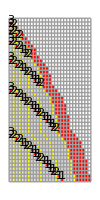
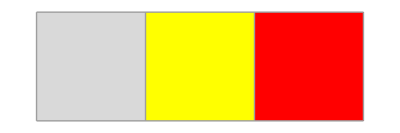
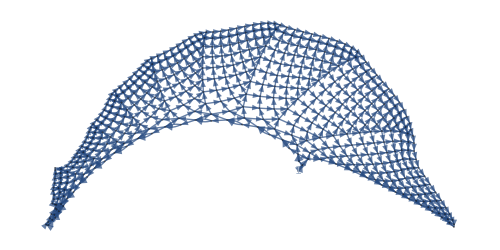
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss3X=SSS[{"BA"->"AB","BC"->"ACB","A"->"BC"},"A",500,SSSMax->44,SSSSize->{100,200},NetSize->{500,250},VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sss3X]
```

3D

{{3D,{1,0,10,1},6
5
3
1,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391 | 484
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{1,0,10,1},6
5
3
1,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391 | 484
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{1,0,9,1},5
5
3
1,5 | 10 | 18 | 30 | 47 | 70 | 100 | 138 | 185 | 242 | 310 | 390
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3D,{2,0,10,1/2},1 | 2
1 | 2
1 | 1
0 | 1,1 | 2 | 4 | 7 | 12 | 19 | 29 | 42 | 59 | 80 | 106 | 137 | 174 | 217
1 | 2 | 3 | 5 | 7 | 10 | 13 | 17 | 21 | 26 | 31 | 37 | 43 | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 |  | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 |  |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss3X["Net"]
```

{{1,1},{1,3},{1,1},{1,2,4},{4,5},{1,1},{1,4,6},{1,6,7},{1,7},{7,8},{1,1},{1,7,9},{1,9,10},{1,10},{1,10,11},2·{{1,11}},{11,12},{1,1},{1,11,13},{1,13,14},{1,14},{1,14,15},2·{{1,15}},{1,15,16},3·{{1,16}},{16,17},{1,1},{1,16,18},{1,18,19},{1,19},{1,19,20},2·{{1,20}},{1,20,21},3·{{1,21}},{1,21,22},4·{{1,22}},{22,23},{1,1},{1,22,24},{1,24,25},{1,25},{1,25,26},2·{{1,26}},{1,26,27},3·{{1,27}},{1,27,28},4·{{1,28}},{1,28,29},5·{{1,29}},{29,30},{1,1},{1,29,31},{1,31,32},{1,32},{1,32,33},2·{{1,33}},{1,33,34},3·{{1,34}},{1,34,35},4·{{1,35}},{1,35,36},5·{{1,36}},{1,36,37},6·{{1,37}},{37,38},{1,1},{1,37,39},{1,39,40},{1,40},{1,40,41},2·{{1,41}},{1,41,42},3·{{1,42}},{1,42,43},4·{{1,43}},{1,43,44},5·{{1,44}},{1,44,45},6·{{1,45}},{1,45,46},7·{{1,46}},{46,47},{1,1},{1,46,48},{1,48,49},{1,49},{1,49,50},2·{{1,50}},{1,50,51},3·{{1,51}},{1,51,52},4·{{1,52}},{1,52,53},5·{{1,53}},{1,53,54},6·{{1,54}},{1,54,55},7·{{1,55}},{1,55,56},8·{{1,56}},{56,57},{1,1},{1,56,58},{1,58,59},{1,59},{1,59,60},2·{{1,60}},{1,60,61},3·{{1,61}},{1,61,62},4·{{1,62}},{1,62,63},5·{{1,63}},{1,63,64},6·{{1,64}},{1,64,65},7·{{1,65}},{1,65,66},8·{{1,66}},{1,66,67},9·{{1,67}},{67,68},{1,1},{1,67,69},{1,69,70},{1,70},{1,70,71},2·{{1,71}},{1,71,72},3·{{1,72}},{1,72,73},4·{{1,73}},{1,73,74},5·{{1,74}},{1,74,75},6·{{1,75}},{1,75,76},7·{{1,76}},{1,76,77},8·{{1,77}},{1,77,78},9·{{1,78}},{1,78,79},10·{{1,79}},{79,80},{1,1},{1,79,81},{1,81,82},{1,82},{1,82,83},2·{{1,83}},{1,83,84},3·{{1,84}},{1,84,85},4·{{1,85}},{1,85,86},5·{{1,86}},{1,86,87},6·{{1,87}},{1,87,88},7·{{1,88}},{1,88,89},8·{{1,89}},{1,89,90},9·{{1,90}},{1,90,91},10·{{1,91}},{1,91,92},11·{{1,92}},{92,93},{1,1},{1,92,94},{1,94,95},{1,95},{1,95,96},2·{{1,96}},{1,96,97},3·{{1,97}},{1,97,98},80·{{1}},{},{1,1},15·{{1}}}

𝕊_(n=1)^∞[]

### 4-d:

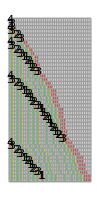
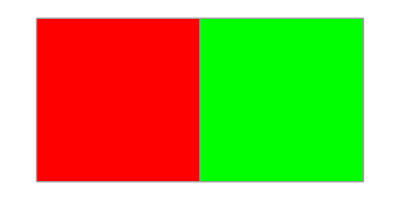
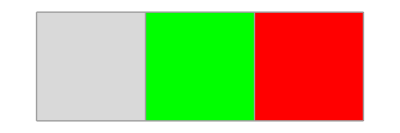
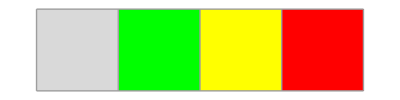
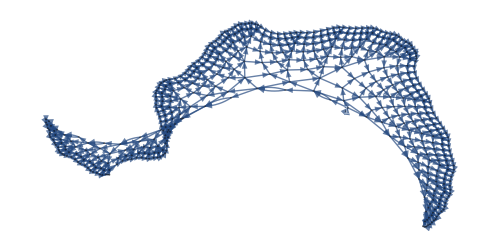
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss4X =SSS[{"BA"->"AB","BD"->"ADB","BC"->"ADCB","A"->"BC"},"A",1000,SSSMax->44,SSSSize->{100,200},NetSize->{500,250},NetMax->500,VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sss4X]
```

4D

{{4D,{1,0,6,1},7
9
9
5
1,7 | 16 | 34 | 66 | 118 | 197 | 311 | 469 | 681 | 958
9 | 18 | 32 | 52 | 79 | 114 | 158 | 212 | 277 | 
9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 |  | 
5 | 6 | 7 | 8 | 9 | 10 | 11 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{1,0,6,1},7
9
9
5
1,7 | 16 | 34 | 66 | 118 | 197 | 311 | 469 | 681 | 958
9 | 18 | 32 | 52 | 79 | 114 | 158 | 212 | 277 | 
9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 |  | 
5 | 6 | 7 | 8 | 9 | 10 | 11 |  |  | 
1 | 1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{1,0,5,1},6
9
9
5
1,6 | 15 | 33 | 65 | 117 | 196 | 310 | 468 | 680
9 | 18 | 32 | 52 | 79 | 114 | 158 | 212 | 
9 | 14 | 20 | 27 | 35 | 44 | 54 |  | 
5 | 6 | 7 | 8 | 9 | 10 |  |  | 
1 | 1 | 1 | 1 | 1 |  |  |  | },{4D,{2,0,6,1/2},1 | 2
1 | 3
2 | 3
1 | 3
2 | -1,1 | 2 | 5 | 11 | 23 | 43 | 75 | 122 | 189 | 280 | 401
1 | 3 | 6 | 12 | 20 | 32 | 47 | 67 | 91 | 121 | 
2 | 3 | 6 | 8 | 12 | 15 | 20 | 24 | 30 |  | 
1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 |  |  | 
2 | -1 | 2 | -1 | 2 | -1 | 2 |  |  |  | }}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss4X["Net"]
```

{{1,1},{1,3,4},{1,1},{1,3,5,6},{1,6,7},{7,8,9},{1,1},{1,8,10,11},{1,11,12},{1,12,13,14},{1,14},{1,14,15},{1,15},{1,15,16},{16,17,18},{1,1},{1,17,19,20},{1,20,21},{1,21,22,23},{1,23},{1,23,24},{1,24},{1,24,25},{1,25,26,27},2·{{1,27}},{1,27,28},2·{{1,28}},{1,28,29},{1,29},{1,29,30},{30,31,32},{1,1},{1,31,33,34},{1,34,35},{1,35,36,37},{1,37},{1,37,38},{1,38},{1,38,39},{1,39,40,41},2·{{1,41}},{1,41,42},2·{{1,42}},{1,42,43},{1,43},{1,43,44},{1,44,45,46},3·{{1,46}},{1,46,47},3·{{1,47}},{1,47,48},2·{{1,48}},{1,48,49},{1,49},{1,49,50},{50,51,52},{1,1},{1,51,53,54},{1,54,55},{1,55,56,57},{1,57},{1,57,58},{1,58},{1,58,59},{1,59,60,61},2·{{1,61}},{1,61,62},2·{{1,62}},{1,62,63},{1,63},{1,63,64},{1,64,65,66},3·{{1,66}},{1,66,67},3·{{1,67}},{1,67,68},2·{{1,68}},{1,68,69},{1,69},{1,69,70},{1,70,71,72},4·{{1,72}},{1,72,73},4·{{1,73}},{1,73,74},3·{{1,74}},{1,74,75},2·{{1,75}},{1,75,76},{1,76},{1,76,77},{77,78,79},{1,1},{1,78,80,81},{1,81,82},{1,82,83,84},{1,84},{1,84,85},{1,85},{1,85,86},{1,86,87,88},2·{{1,88}},{1,88,89},2·{{1,89}},{1,89,90},{1,90},{1,90,91},{1,91,92,93},3·{{1,93}},{1,93,94},3·{{1,94}},{1,94,95},2·{{1,95}},{1,95,96},{1,96},{1,96,97},{1,97,98,99},4·{{1,99}},{1,99,100},4·{{1,100}},{1,100,101},3·{{1,101}},{1,101,102},2·{{1,102}},{1,102,103},{1,103},{1,103,104},{1,104,105,106},5·{{1,106}},{1,106,107},5·{{1,107}},{1,107,108},4·{{1,108}},{1,108,109},3·{{1,109}},{1,109,110},2·{{1,110}},{1,110,111},{1,111},{1,111,112},{112,113,114},{1,1},{1,113,115,116},{1,116,117},{1,117,118,119},{1,119},{1,119,120},{1,120},{1,120,121},{1,121,122,123},2·{{1,123}},{1,123,124},2·{{1,124}},{1,124,125},{1,125},{1,125,126},{1,126,127,128},3·{{1,128}},{1,128,129},3·{{1,129}},{1,129,130},2·{{1,130}},{1,130,131},{1,131},{1,131,132},{1,132,133,134},4·{{1,134}},{1,134,135},4·{{1,135}},{1,135,136},3·{{1,136}},{1,136,137},2·{{1,137}},{1,137,138},{1,138},{1,138,139},{1,139,140,141},5·{{1,141}},{1,141,142},5·{{1,142}},{1,142,143},4·{{1,143}},{1,143,144},3·{{1,144}},{1,144,145},2·{{1,145}},{1,145,146},{1,146},{1,146,147},{1,147,148,149},6·{{1,149}},{1,149,150},6·{{1,150}},{1,150,151},5·{{1,151}},{1,151,152},4·{{1,152}},{1,152,153},3·{{1,153}},{1,153,154},2·{{1,154}},{1,154,155},{1,155},{1,155,156},{156,157,158},{1,1},{1,157,159,160},{1,160,161},{1,161,162,163},{1,163},{1,163,164},{1,164},{1,164,165},{1,165,166,167},2·{{1,167}},{1,167,168},2·{{1,168}},{1,168,169},{1,169},{1,169,170},{1,170,171,172},3·{{1,172}},{1,172,173},3·{{1,173}},{1,173,174},2·{{1,174}},{1,174,175},{1,175},{1,175,176},{1,176,177,178},4·{{1,178}},{1,178,179},4·{{1,179}},{1,179,180},3·{{1,180}},{1,180,181},2·{{1,181}},{1,181,182},{1,182},{1,182,183},{1,183,184,185},5·{{1,185}},{1,185,186},5·{{1,186}},{1,186,187},4·{{1,187}},{1,187,188},3·{{1,188}},{1,188,189},2·{{1,189}},{1,189,190},{1,190},{1,190,191},{1,191,192,193},6·{{1,193}},{1,193,194},6·{{1,194}},{1,194,195},5·{{1,195}},{1,195,196},4·{{1,196}},{1,196,197},3·{{1,197}},{1,197,198},2·{{1,198}},{1,198,199},{1,199},{1,199,200},{1,200,201,202},7·{{1,202}},{1,202,203},7·{{1,203}},{1,203,204},6·{{1,204}},{1,204,205},5·{{1,205}},{1,205,206},4·{{1,206}},{1,206,207},3·{{1,207}},{1,207,208},2·{{1,208}},{1,208,209},{1,209},{1,209,210},{210,211,212},{1,1},{1,211,213,214},{1,214,215},{1,215,216,217},{1,217},{1,217,218},{1,218},{1,218,219},{1,219,220,221},2·{{1,221}},{1,221,222},2·{{1,222}},{1,222,223},{1,223},{1,223,224},{1,224,225,226},3·{{1,226}},{1,226,227},3·{{1,227}},{1,227,228},2·{{1,228}},{1,228,229},{1,229},{1,229,230},{1,230,231,232},4·{{1,232}},{1,232,233},4·{{1,233}},{1,233,234},3·{{1,234}},{1,234,235},2·{{1,235}},{1,235,236},{1,236},{1,236,237},{1,237,238,239},5·{{1,239}},{1,239,240},5·{{1,240}},{1,240,241},4·{{1,241}},{1,241,242},3·{{1,242}},{1,242,243},2·{{1,243}},{1,243,244},{1,244},{1,244,245},{1,245,246,247},6·{{1,247}},{1,247,248},6·{{1,248}},{1,248,249},5·{{1,249}},{1,249,250},4·{{1,250}},{1,250,251},3·{{1,251}},{1,251,252},2·{{1,252}},{1,252,253},{1,253},{1,253,254},{1,254,255,256},7·{{1,256}},{1,256,257},7·{{1,257}},{1,257,258},6·{{1,258}},{1,258,259},5·{{1,259}},{1,259,260},4·{{1,260}},{1,260,261},3·{{1,261}},{1,261,262},2·{{1,262}},{1,262,263},{1,263},{1,263,264},{1,264,265,266},8·{{1,266}},{1,266,267},8·{{1,267}},{1,267,268},7·{{1,268}},{1,268,269},6·{{1,269}},{1,269,270},5·{{1,270}},{1,270,271},4·{{1,271}},{1,271,272},3·{{1,272}},{1,272,273},2·{{1,273}},{1,273,274},{1,274},{1,274,275},{275,276,277},{1,1},{1,276,278,279},{1,279,280},{1,280,281,282},{1,282},{1,282,283},{1,283},{1,283,284},{1,284,285,286},2·{{1,286}},{1,286,287},2·{{1,287}},{1,287,288},{1,288},{1,288,289},{1,289,290,291},3·{{1,291}},{1,291,292},3·{{1,292}},{1,292,293},{1,293},249·{{1}},{},{1,1},41·{{1}}}

-Graphics-

𝕊_(n=1)^∞[{1,1},{1,i_n-1,i_n+1,i_n+2},b,c,𝕊_(y=1)^(n-1)[𝕊_(x=1)^y[x·a,b,1],b,c],2·a,{i_(n+1)}]]

…

### 5-d:

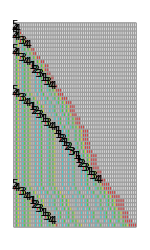
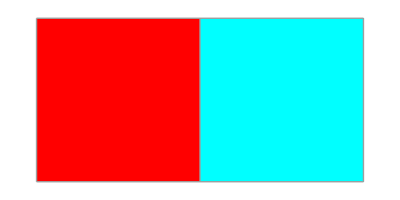
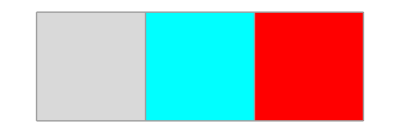
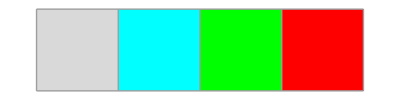
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss5X=SSS[{"BA"->"AB","BE"->"AEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",1500,SSSMax->50,SSSSize->{150,250},NetSize->{500,300},VertexLabels->{x_:>Placed[x,Tooltip],
1->Placed[Text[Framed[1,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->15]],Center]}];
```

```mathematica
GuessDimension[sss5X]
```

Part::partw: Part 1 of {} does not exist.

{}

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets[sss5X[["Net"]]]
```

```mathematica
temp5={{1,1},{1,3,4},{1,1},{1,3,5,6},{1,6,7,8},{8,9,10},{1,1},{1,9,11,12},{1,12,13,14},{1,14,15,16},{1,16},{1,16,17},{1,17,18,19},{1,19},{1,19,20,21},{21,22,23},{1,1},{1,22,24,25},{1,25,26,27},{1,27,28,29},{1,29},{1,29,30},{1,30,31,32},{1,32},{1,32,33,34},{1,34,35,36},2·{{1,36}},{1,36,37},{1,37},{1,37,38},{1,38,39,40},2·{{1,40}},{1,40,41},{1,41,42,43},{1,43},{1,43,44,45},{45,46,47},{1,1},{1,46,48,49},{1,49,50,51},{1,51,52,53},{1,53},{1,53,54},{1,54,55,56},{1,56},{1,56,57,58},{1,58,59,60},2·{{1,60}},{1,60,61},{1,61},{1,61,62},{1,62,63,64},2·{{1,64}},{1,64,65},{1,65,66,67},{1,67},{1,67,68,69},{1,69,70,71},3·{{1,71}},{1,71,72},2·{{1,72}},{1,72,73},{1,73},{1,73,74},{1,74,75,76},3·{{1,76}},{1,76,77},{1,77},{1,77,78},{1,78,79,80},2·{{1,80}},{1,80,81},{1,81,82,83},{1,83},{1,83,84,85},{85,86,87},{1,1},{1,86,88,89},{1,89,90,91},{1,91,92,93},{1,93},{1,93,94},{1,94,95,96},{1,96},{1,96,97,98},{1,98,99,100},2·{{1,100}},{1,100,101},{1,101},{1,101,102},{1,102,103,104},2·{{1,104}},{1,104,105},{1,105,106,107},{1,107},{1,107,108,109},{1,109,110,111},3·{{1,111}},{1,111,112},2·{{1,112}},{1,112,113},{1,113},{1,113,114},{1,114,115,116},3·{{1,116}},{1,116,117},{1,117},{1,117,118},{1,118,119,120},2·{{1,120}},{1,120,121},{1,121,122,123},{1,123},{1,123,124,125},{1,125,126,127},4·{{1,127}},{1,127,128},3·{{1,128}},{1,128,129},2·{{1,129}},{1,129,130},{1,130},{1,130,131},{1,131,132,133},4·{{1,133}},{1,133,134},2·{{1,134}},{1,134,135},{1,135},{1,135,136},{1,136,137,138},3·{{1,138}},{1,138,139},{1,139},{1,139,140},{1,140,141,142},2·{{1,142}},{1,142,143},{1,143,144,145},{1,145},{1,145,146,147},{147,148,149},{1,1},{1,148,150,151},{1,151,152,153},{1,153,154,155},{1,155},{1,155,156},{1,156,157,158},{1,158},{1,158,159,160},{1,160,161,162},2·{{1,162}},{1,162,163},{1,163},{1,163,164},{1,164,165,166},2·{{1,166}},{1,166,167},{1,167,168,169},{1,169},{1,169,170,171},{1,171,172,173},3·{{1,173}},{1,173,174},2·{{1,174}},{1,174,175},{1,175},{1,175,176},{1,176,177,178},3·{{1,178}},{1,178,179},{1,179},{1,179,180},{1,180,181,182},2·{{1,182}},{1,182,183},{1,183,184,185},{1,185},{1,185,186,187},{1,187,188,189},4·{{1,189}},{1,189,190},3·{{1,190}},{1,190,191},2·{{1,191}},{1,191,192},{1,192},{1,192,193},{1,193,194,195},4·{{1,195}},{1,195,196},2·{{1,196}},{1,196,197},{1,197},{1,197,198},{1,198,199,200},3·{{1,200}},{1,200,201},{1,201},{1,201,202},{1,202,203,204},2·{{1,204}},{1,204,205},{1,205,206,207},{1,207},{1,207,208,209},{1,209,210,211},5·{{1,211}},{1,211,212},4·{{1,212}},{1,212,213},3·{{1,213}},{1,213,214},2·{{1,214}},{1,214,215},{1,215},{1,215,216},{1,216,217,218},5·{{1,218}},{1,218,219},3·{{1,219}},{1,219,220},2·{{1,220}},{1,220,221},{1,221},{1,221,222},{1,222,223,224},4·{{1,224}},{1,224,225},2·{{1,225}},{1,225,226},{1,226},{1,226,227},{1,227,228,229},3·{{1,229}},{1,229,230},{1,230},{1,230,231},{1,231,232,233},2·{{1,233}},{1,233,234},{1,234,235,236},{1,236},{1,236,237,238},{238,239,240},{1,1},{1,239,241,242},{1,242,243,244},{1,244,245,246},{1,246},{1,246,247},{1,247,248,249},{1,249},{1,249,250,251},{1,251,252,253},2·{{1,253}},{1,253,254},{1,254},{1,254,255},{1,255,256,257},2·{{1,257}},{1,257,258},{1,258,259,260},{1,260},{1,260,261,262},{1,262,263,264},3·{{1,264}},{1,264,265},2·{{1,265}},{1,265,266},{1,266},{1,266,267},{1,267,268,269},3·{{1,269}},{1,269,270},{1,270},{1,270,271},{1,271,272,273},2·{{1,273}},{1,273,274},{1,274,275,276},{1,276},{1,276,277,278},{1,278,279,280},4·{{1,280}},{1,280,281},3·{{1,281}},{1,281,282},2·{{1,282}},{1,282,283},{1,283},{1,283,284},{1,284,285,286},4·{{1,286}},{1,286,287},2·{{1,287}},{1,287,288},{1,288},{1,288,289},{1,289,290,291},3·{{1,291}},{1,291,292},{1,292},{1,292,293},{1,293,294,295},2·{{1,295}},{1,295,296},{1,296,297,298},{1,298},{1,298,299,300},{1,300,301,302},5·{{1,302}},{1,302,303},4·{{1,303}},{1,303,304},3·{{1,304}},{1,304,305},2·{{1,305}},{1,305,306},{1,306},{1,306,307},{1,307,308,309},5·{{1,309}},{1,309,310},3·{{1,310}},{1,310,311},2·{{1,311}},{1,311,312},{1,312},{1,312,313},{1,313,314,315},4·{{1,315}},{1,315,316},2·{{1,316}},{1,316,317},{1,317},{1,317,318},{1,318,319,320},3·{{1,320}},{1,320,321},{1,321},{1,321,322},{1,322,323,324},2·{{1,324}},{1,324,325},{1,325,326,327},{1,327},{1,327,328,329},{1,329,330,331},6·{{1,331}},{1,331,332},5·{{1,332}},{1,332,333},4·{{1,333}},{1,333,334},3·{{1,334}},{1,334,335},2·{{1,335}},{1,335,336},{1,336},{1,336,337},{1,337,338,339},6·{{1,339}},{1,339,340},4·{{1,340}},{1,340,341},3·{{1,341}},{1,341,342},2·{{1,342}},{1,342,343},{1,343},{1,343,344},{1,344,345,346},5·{{1,346}},{1,346,347},3·{{1,347}},{1,347,348},2·{{1,348}},{1,348,349},{1,349},{1,349,350},{1,350,351,352},4·{{1,352}},{1,352,353},2·{{1,353}},{1,353,354},{1,354},{1,354,355},{1,355,356,357},3·{{1,357}},{1,357,358},{1,358},{1,358,359},{1,359,360,361},2·{{1,361}},{1,361,362},{1,362,363,364},{1,364},{1,364,365,366},{366,367,368},{1,1},{1,367,369,370},{1,370,371,372},{1,372,373,374},{1,374},{1,374,375},{1,375,376,377},{1,377},{1,377,378,379},{1,379,380,381},2·{{1,381}},{1,381,382},{1,382},{1,382,383},{1,383,384,385},2·{{1,385}},{1,385,386},{1,386,387,388},{1,388},{1,388,389,390},{1,390,391,392},3·{{1,392}},{1,392,393},2·{{1,393}},{1,393,394},{1,394},{1,394,395},{1,395,396,397},3·{{1,397}},{1,397,398},{1,398},{1,398,399},{1,399,400,401},2·{{1,401}},{1,401,402},{1,402,403,404},{1,404},{1,404,405,406},{1,406,407,408},4·{{1,408}},{1,408,409},3·{{1,409}},{1,409,410},2·{{1,410}},{1,410,411},{1,411},{1,411,412},{1,412,413,414},4·{{1,414}},{1,414,415},2·{{1,415}},{1,415,416},{1,416},{1,416,417},{1,417,418,419},3·{{1,419}},{1,419,420},{1,420},{1,420,421},{1,421,422,423},2·{{1,423}},{1,423,424},{1,424,425,426},{1,426},{1,426,427,428},{1,428,429,430},5·{{1,430}},{1,430,431},4·{{1,431}},{1,431,432},3·{{1,432}},{1,432,433},2·{{1,433}},{1,433,434},{1,434},{1,434,435},{1,435,436,437},5·{{1,437}},{1,437,438},3·{{1,438}},{1,438,439},2·{{1,439}},{1,439,440},{1,440},{1,440,441},{1,441,442,443},4·{{1,443}},{1,443,444},2·{{1,444}},{1,444,445},{1,445},{1,445,446},{1,446,447,448},3·{{1,448}},{1,448,449},{1,449},{1,449,450},{1,450,451,452},2·{{1,452}},{1,452,453},{1,453,454,455},{1,455},{1,455,456,457},{1,457,458,459},6·{{1,459}},{1,459,460},5·{{1,460}},{1,460,461},4·{{1,461}},{1,461,462},3·{{1,462}},{1,462,463},2·{{1,463}},{1,463,464},{1,464},{1,464,465},{1,465,466,467},6·{{1,467}},{1,467,468},4·{{1,468}},{1,468,469},3·{{1,469}},{1,469,470},2·{{1,470}},{1,470,471},{1,471},{1,471,472},{1,472,473,474},5·{{1,474}},{1,474,475},3·{{1,475}},{1,475,476},2·{{1,476}},{1,476,477},{1,477},{1,477,478},{1,478,479,480},4·{{1,480}},{1,480,481},2·{{1,481}},{1,481,482},{1,482},{1,482,483},{1,483,484,485},3·{{1,485}},{1,485,486},{1,486},{1,486,487},{1,487,488,489},2·{{1,489}},{1,489,490},{1,490,491,492},{1,492},{1,492,493,494},{1,494,495,496},7·{{1,496}},{1,496,497},6·{{1,497}},{1,497,498},5·{{1,498}},{1,498,499},4·{{1,499}},{1,499,500},3·{{1,500}},{1,500,501},2·{{1,501}},{1,501,502},{1,502},{1,502,503},{1,503,504,505},7·{{1,505}},{1,505,506},5·{{1,506}},{1,506,507},4·{{1,507}},{1,507,508},3·{{1,508}},{1,508,509},2·{{1,509}},{1,509,510},{1,510},{1,510,511},{1,511,512,513},6·{{1,513}},{1,513,514},4·{{1,514}},{1,514,515},3·{{1,515}},{1,515,516},2·{{1,516}},{1,516,517},{1,517},{1,517,518},{1,518,519,520},5·{{1,520}},{1,520,521},3·{{1,521}},{1,521,522},2·{{1,522}},{1,522,523},{1,523},{1,523,524},{1,524,525,526},4·{{1,526}},{1,526,527},2·{{1,527}},{1,527,528},{1,528},{1,528,529},{1,529,530,531},3·{{1,531}},{1,531,532},{1,532},{1,532,533},{1,533,534,535},2·{{1,535}},{1,535,536},{1,536,537,538},{1,538},{1,538,539,540},{540,541,542},{1,1},{1,541,543,544},{1,544,545,546},{1,546,547,548},{1,548},{1,548,549},{1,549,550,551},{1,551},{1,551,552,553},{1,553,554,555},2·{{1,555}},{1,555,556},{1,556},527·{{1}},{},{1,1},26·{{1}}};
```

```mathematica
Cases[temp5 ,{1,_}]
```

{{1,1},{1,1},{1,1},{1,16},{1,19},{1,1},{1,29},{1,32},{1,37},{1,43},{1,1},{1,53},{1,56},{1,61},{1,67},{1,73},{1,77},{1,83},{1,1},{1,93},{1,96},{1,101},{1,107},{1,113},{1,117},{1,123},{1,130},{1,135},{1,139},{1,145},{1,1},{1,155},{1,158},{1,163},{1,169},{1,175},{1,179},{1,185},{1,192},{1,197},{1,201},{1,207},{1,215},{1,221},{1,226},{1,230},{1,236},{1,1},{1,246},{1,249},{1,254},{1,260},{1,266},{1,270},{1,276},{1,283},{1,288},{1,292},{1,298},{1,306},{1,312},{1,317},{1,321},{1,327},{1,336},{1,343},{1,349},{1,354},{1,358},{1,364},{1,1},{1,374},{1,377},{1,382},{1,388},{1,394},{1,398},{1,404},{1,411},{1,416},{1,420},{1,426},{1,434},{1,440},{1,445},{1,449},{1,455},{1,464},{1,471},{1,477},{1,482},{1,486},{1,492},{1,502},{1,510},{1,517},{1,523},{1,528},{1,532},{1,538},{1,1},{1,548},{1,551},{1,556},{1,1}}

```mathematica
Last/@%
```

{1,1,1,16,19,1,29,32,37,43,1,53,56,61,67,73,77,83,1,93,96,101,107,113,117,123,130,135,139,145,1,155,158,163,169,175,179,185,192,197,201,207,215,221,226,230,236,1,246,249,254,260,266,270,276,283,288,292,298,306,312,317,321,327,336,343,349,354,358,364,1,374,377,382,388,394,398,404,411,416,420,426,434,440,445,449,455,464,471,477,482,486,492,502,510,517,523,528,532,538,1,548,551,556,1}

```mathematica
Select[%120,#!=1&]
```

{16,19,29,32,37,43,53,56,61,67,73,77,83,93,96,101,107,113,117,123,130,135,139,145,155,158,163,169,175,179,185,192,197,201,207,215,221,226,230,236,246,249,254,260,266,270,276,283,288,292,298,306,312,317,321,327,336,343,349,354,358,364,374,377,382,388,394,398,404,411,416,420,426,434,440,445,449,455,464,471,477,482,486,492,502,510,517,523,528,532,538,548,551,556}

```mathematica
CheckDimension[%]
```

{failed,16 | 19 | 29 | 32 | 37 | 43 | 53 | 56 | 61 | 67 | 73 | 77 | 83 | 93 | 96 | 101 | 107 | 113 | 117 | 123 | 130 | 135 | 139 | 145 | 155 | 158 | 163 | 169 | 175 | 179 | 185 | 192 | 197 | 201 | 207 | 215 | 221 | 226 | 230 | 236 | 246 | 249 | 254 | 260 | 266 | 270 | 276 | 283 | 288 | 292 | 298 | 306 | 312 | 317 | 321 | 327 | 336 | 343 | 349 | 354 | 358 | 364 | 374 | 377 | 382 | 388 | 394 | 398 | 404 | 411 | 416 | 420 | 426 | 434 | 440 | 445 | 449 | 455 | 464 | 471 | 477 | 482 | 486 | 492 | 502 | 510 | 517 | 523 | 528 | 532 | 538 | 548 | 551 | 556
3 | 10 | 3 | 5 | 6 | 10 | 3 | 5 | 6 | 6 | 4 | 6 | 10 | 3 | 5 | 6 | 6 | 4 | 6 | 7 | 5 | 4 | 6 | 10 | 3 | 5 | 6 | 6 | 4 | 6 | 7 | 5 | 4 | 6 | 8 | 6 | 5 | 4 | 6 | 10 | 3 | 5 | 6 | 6 | 4 | 6 | 7 | 5 | 4 | 6 | 8 | 6 | 5 | 4 | 6 | 9 | 7 | 6 | 5 | 4 | 6 | 10 | 3 | 5 | 6 | 6 | 4 | 6 | 7 | 5 | 4 | 6 | 8 | 6 | 5 | 4 | 6 | 9 | 7 | 6 | 5 | 4 | 6 | 10 | 8 | 7 | 6 | 5 | 4 | 6 | 10 | 3 | 5 | 
7 | -7 | 2 | 1 | 4 | -7 | 2 | 1 | 0 | -2 | 2 | 4 | -7 | 2 | 1 | 0 | -2 | 2 | 1 | -2 | -1 | 2 | 4 | -7 | 2 | 1 | 0 | -2 | 2 | 1 | -2 | -1 | 2 | 2 | -2 | -1 | -1 | 2 | 4 | -7 | 2 | 1 | 0 | -2 | 2 | 1 | -2 | -1 | 2 | 2 | -2 | -1 | -1 | 2 | 3 | -2 | -1 | -1 | -1 | 2 | 4 | -7 | 2 | 1 | 0 | -2 | 2 | 1 | -2 | -1 | 2 | 2 | -2 | -1 | -1 | 2 | 3 | -2 | -1 | -1 | -1 | 2 | 4 | -2 | -1 | -1 | -1 | -1 | 2 | 4 | -7 | 2 |  | 
-14 | 9 | -1 | 3 | -11 | 9 | -1 | -1 | -2 | 4 | 2 | -11 | 9 | -1 | -1 | -2 | 4 | -1 | -3 | 1 | 3 | 2 | -11 | 9 | -1 | -1 | -2 | 4 | -1 | -3 | 1 | 3 | 0 | -4 | 1 | 0 | 3 | 2 | -11 | 9 | -1 | -1 | -2 | 4 | -1 | -3 | 1 | 3 | 0 | -4 | 1 | 0 | 3 | 1 | -5 | 1 | 0 | 0 | 3 | 2 | -11 | 9 | -1 | -1 | -2 | 4 | -1 | -3 | 1 | 3 | 0 | -4 | 1 | 0 | 3 | 1 | -5 | 1 | 0 | 0 | 3 | 2 | -6 | 1 | 0 | 0 | 0 | 3 | 2 | -11 | 9 |  |  | 
23 | -10 | 4 | -14 | 20 | -10 | 0 | -1 | 6 | -2 | -13 | 20 | -10 | 0 | -1 | 6 | -5 | -2 | 4 | 2 | -1 | -13 | 20 | -10 | 0 | -1 | 6 | -5 | -2 | 4 | 2 | -3 | -4 | 5 | -1 | 3 | -1 | -13 | 20 | -10 | 0 | -1 | 6 | -5 | -2 | 4 | 2 | -3 | -4 | 5 | -1 | 3 | -2 | -6 | 6 | -1 | 0 | 3 | -1 | -13 | 20 | -10 | 0 | -1 | 6 | -5 | -2 | 4 | 2 | -3 | -4 | 5 | -1 | 3 | -2 | -6 | 6 | -1 | 0 | 3 | -1 | -8 | 7 | -1 | 0 | 0 | 3 | -1 | -13 | 20 |  |  |  | 
-33 | 14 | -18 | 34 | -30 | 10 | -1 | 7 | -8 | -11 | 33 | -30 | 10 | -1 | 7 | -11 | 3 | 6 | -2 | -3 | -12 | 33 | -30 | 10 | -1 | 7 | -11 | 3 | 6 | -2 | -5 | -1 | 9 | -6 | 4 | -4 | -12 | 33 | -30 | 10 | -1 | 7 | -11 | 3 | 6 | -2 | -5 | -1 | 9 | -6 | 4 | -5 | -4 | 12 | -7 | 1 | 3 | -4 | -12 | 33 | -30 | 10 | -1 | 7 | -11 | 3 | 6 | -2 | -5 | -1 | 9 | -6 | 4 | -5 | -4 | 12 | -7 | 1 | 3 | -4 | -7 | 15 | -8 | 1 | 0 | 3 | -4 | -12 | 33 |  |  |  |  | 
47 | -32 | 52 | -64 | 40 | -11 | 8 | -15 | -3 | 44 | -63 | 40 | -11 | 8 | -18 | 14 | 3 | -8 | -1 | -9 | 45 | -63 | 40 | -11 | 8 | -18 | 14 | 3 | -8 | -3 | 4 | 10 | -15 | 10 | -8 | -8 | 45 | -63 | 40 | -11 | 8 | -18 | 14 | 3 | -8 | -3 | 4 | 10 | -15 | 10 | -9 | 1 | 16 | -19 | 8 | 2 | -7 | -8 | 45 | -63 | 40 | -11 | 8 | -18 | 14 | 3 | -8 | -3 | 4 | 10 | -15 | 10 | -9 | 1 | 16 | -19 | 8 | 2 | -7 | -3 | 22 | -23 | 9 | -1 | 3 | -7 | -8 | 45 |  |  |  |  |  | 
-79 | 84 | -116 | 104 | -51 | 19 | -23 | 12 | 47 | -107 | 103 | -51 | 19 | -26 | 32 | -11 | -11 | 7 | -8 | 54 | -108 | 103 | -51 | 19 | -26 | 32 | -11 | -11 | 5 | 7 | 6 | -25 | 25 | -18 | 0 | 53 | -108 | 103 | -51 | 19 | -26 | 32 | -11 | -11 | 5 | 7 | 6 | -25 | 25 | -19 | 10 | 15 | -35 | 27 | -6 | -9 | -1 | 53 | -108 | 103 | -51 | 19 | -26 | 32 | -11 | -11 | 5 | 7 | 6 | -25 | 25 | -19 | 10 | 15 | -35 | 27 | -6 | -9 | 4 | 25 | -45 | 32 | -10 | 4 | -10 | -1 | 53 |  |  |  |  |  |  | 
163 | -200 | 220 | -155 | 70 | -42 | 35 | 35 | -154 | 210 | -154 | 70 | -45 | 58 | -43 | 0 | 18 | -15 | 62 | -162 | 211 | -154 | 70 | -45 | 58 | -43 | 0 | 16 | 2 | -1 | -31 | 50 | -43 | 18 | 53 | -161 | 211 | -154 | 70 | -45 | 58 | -43 | 0 | 16 | 2 | -1 | -31 | 50 | -44 | 29 | 5 | -50 | 62 | -33 | -3 | 8 | 54 | -161 | 211 | -154 | 70 | -45 | 58 | -43 | 0 | 16 | 2 | -1 | -31 | 50 | -44 | 29 | 5 | -50 | 62 | -33 | -3 | 13 | 21 | -70 | 77 | -42 | 14 | -14 | 9 | 54 |  |  |  |  |  |  |  | 
-363 | 420 | -375 | 225 | -112 | 77 | 0 | -189 | 364 | -364 | 224 | -115 | 103 | -101 | 43 | 18 | -33 | 77 | -224 | 373 | -365 | 224 | -115 | 103 | -101 | 43 | 16 | -14 | -3 | -30 | 81 | -93 | 61 | 35 | -214 | 372 | -365 | 224 | -115 | 103 | -101 | 43 | 16 | -14 | -3 | -30 | 81 | -94 | 73 | -24 | -55 | 112 | -95 | 30 | 11 | 46 | -215 | 372 | -365 | 224 | -115 | 103 | -101 | 43 | 16 | -14 | -3 | -30 | 81 | -94 | 73 | -24 | -55 | 112 | -95 | 30 | 16 | 8 | -91 | 147 | -119 | 56 | -28 | 23 | 45 |  |  |  |  |  |  |  |  | 
783 | -795 | 600 | -337 | 189 | -77 | -189 | 553 | -728 | 588 | -339 | 218 | -204 | 144 | -25 | -51 | 110 | -301 | 597 | -738 | 589 | -339 | 218 | -204 | 144 | -27 | -30 | 11 | -27 | 111 | -174 | 154 | -26 | -249 | 586 | -737 | 589 | -339 | 218 | -204 | 144 | -27 | -30 | 11 | -27 | 111 | -175 | 167 | -97 | -31 | 167 | -207 | 125 | -19 | 35 | -261 | 587 | -737 | 589 | -339 | 218 | -204 | 144 | -27 | -30 | 11 | -27 | 111 | -175 | 167 | -97 | -31 | 167 | -207 | 125 | -14 | -8 | -99 | 238 | -266 | 175 | -84 | 51 | 22 |  |  |  |  |  |  |  |  |  | 
-1578 | 1395 | -937 | 526 | -266 | -112 | 742 | -1281 | 1316 | -927 | 557 | -422 | 348 | -169 | -26 | 161 | -411 | 898 | -1335 | 1327 | -928 | 557 | -422 | 348 | -171 | -3 | 41 | -38 | 138 | -285 | 328 | -180 | -223 | 835 | -1323 | 1326 | -928 | 557 | -422 | 348 | -171 | -3 | 41 | -38 | 138 | -286 | 342 | -264 | 66 | 198 | -374 | 332 | -144 | 54 | -296 | 848 | -1324 | 1326 | -928 | 557 | -422 | 348 | -171 | -3 | 41 | -38 | 138 | -286 | 342 | -264 | 66 | 198 | -374 | 332 | -139 | 6 | -91 | 337 | -504 | 441 | -259 | 135 | -29 |  |  |  |  |  |  |  |  |  |  | 
2973 | -2332 | 1463 | -792 | 154 | 854 | -2023 | 2597 | -2243 | 1484 | -979 | 770 | -517 | 143 | 187 | -572 | 1309 | -2233 | 2662 | -2255 | 1485 | -979 | 770 | -519 | 168 | 44 | -79 | 176 | -423 | 613 | -508 | -43 | 1058 | -2158 | 2649 | -2254 | 1485 | -979 | 770 | -519 | 168 | 44 | -79 | 176 | -424 | 628 | -606 | 330 | 132 | -572 | 706 | -476 | 198 | -350 | 1144 | -2172 | 2650 | -2254 | 1485 | -979 | 770 | -519 | 168 | 44 | -79 | 176 | -424 | 628 | -606 | 330 | 132 | -572 | 706 | -471 | 145 | -97 | 428 | -841 | 945 | -700 | 394 | -164 |  |  |  |  |  |  |  |  |  |  |  | 
-5305 | 3795 | -2255 | 946 | 700 | -2877 | 4620 | -4840 | 3727 | -2463 | 1749 | -1287 | 660 | 44 | -759 | 1881 | -3542 | 4895 | -4917 | 3740 | -2464 | 1749 | -1289 | 687 | -124 | -123 | 255 | -599 | 1036 | -1121 | 465 | 1101 | -3216 | 4807 | -4903 | 3739 | -2464 | 1749 | -1289 | 687 | -124 | -123 | 255 | -600 | 1052 | -1234 | 936 | -198 | -704 | 1278 | -1182 | 674 | -548 | 1494 | -3316 | 4822 | -4904 | 3739 | -2464 | 1749 | -1289 | 687 | -124 | -123 | 255 | -600 | 1052 | -1234 | 936 | -198 | -704 | 1278 | -1177 | 616 | -242 | 525 | -1269 | 1786 | -1645 | 1094 | -558 |  |  |  |  |  |  |  |  |  |  |  |  | 
9100 | -6050 | 3201 | -246 | -3577 | 7497 | -9460 | 8567 | -6190 | 4212 | -3036 | 1947 | -616 | -803 | 2640 | -5423 | 8437 | -9812 | 8657 | -6204 | 4213 | -3038 | 1976 | -811 | 1 | 378 | -854 | 1635 | -2157 | 1586 | 636 | -4317 | 8023 | -9710 | 8642 | -6203 | 4213 | -3038 | 1976 | -811 | 1 | 378 | -855 | 1652 | -2286 | 2170 | -1134 | -506 | 1982 | -2460 | 1856 | -1222 | 2042 | -4810 | 8138 | -9726 | 8643 | -6203 | 4213 | -3038 | 1976 | -811 | 1 | 378 | -855 | 1652 | -2286 | 2170 | -1134 | -506 | 1982 | -2455 | 1793 | -858 | 767 | -1794 | 3055 | -3431 | 2739 | -1652 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-15150 | 9251 | -3447 | -3331 | 11074 | -16957 | 18027 | -14757 | 10402 | -7248 | 4983 | -2563 | -187 | 3443 | -8063 | 13860 | -18249 | 18469 | -14861 | 10417 | -7251 | 5014 | -2787 | 812 | 377 | -1232 | 2489 | -3792 | 3743 | -950 | -4953 | 12340 | -17733 | 18352 | -14845 | 10416 | -7251 | 5014 | -2787 | 812 | 377 | -1233 | 2507 | -3938 | 4456 | -3304 | 628 | 2488 | -4442 | 4316 | -3078 | 3264 | -6852 | 12948 | -17864 | 18369 | -14846 | 10416 | -7251 | 5014 | -2787 | 812 | 377 | -1233 | 2507 | -3938 | 4456 | -3304 | 628 | 2488 | -4437 | 4248 | -2651 | 1625 | -2561 | 4849 | -6486 | 6170 | -4391 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
24401 | -12698 | 116 | 14405 | -28031 | 34984 | -32784 | 25159 | -17650 | 12231 | -7546 | 2376 | 3630 | -11506 | 21923 | -32109 | 36718 | -33330 | 25278 | -17668 | 12265 | -7801 | 3599 | -435 | -1609 | 3721 | -6281 | 7535 | -4693 | -4003 | 17293 | -30073 | 36085 | -33197 | 25261 | -17667 | 12265 | -7801 | 3599 | -435 | -1610 | 3740 | -6445 | 8394 | -7760 | 3932 | 1860 | -6930 | 8758 | -7394 | 6342 | -10116 | 19800 | -30812 | 36233 | -33215 | 25262 | -17667 | 12265 | -7801 | 3599 | -435 | -1610 | 3740 | -6445 | 8394 | -7760 | 3932 | 1860 | -6925 | 8685 | -6899 | 4276 | -4186 | 7410 | -11335 | 12656 | -10561 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-37099 | 12814 | 14289 | -42436 | 63015 | -67768 | 57943 | -42809 | 29881 | -19777 | 9922 | 1254 | -15136 | 33429 | -54032 | 68827 | -70048 | 58608 | -42946 | 29933 | -20066 | 11400 | -4034 | -1174 | 5330 | -10002 | 13816 | -12228 | 690 | 21296 | -47366 | 66158 | -69282 | 58458 | -42928 | 29932 | -20066 | 11400 | -4034 | -1175 | 5350 | -10185 | 14839 | -16154 | 11692 | -2072 | -8790 | 15688 | -16152 | 13736 | -16458 | 29916 | -50612 | 67045 | -69448 | 58477 | -42929 | 29932 | -20066 | 11400 | -4034 | -1175 | 5350 | -10185 | 14839 | -16154 | 11692 | -2072 | -8785 | 15610 | -15584 | 11175 | -8462 | 11596 | -18745 | 23991 | -23217 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
49913 | 1475 | -56725 | 105451 | -130783 | 125711 | -100752 | 72690 | -49658 | 29699 | -8668 | -16390 | 48565 | -87461 | 122859 | -138875 | 128656 | -101554 | 72879 | -49999 | 31466 | -15434 | 2860 | 6504 | -15332 | 23818 | -26044 | 12918 | 20606 | -68662 | 113524 | -135440 | 127740 | -101386 | 72860 | -49998 | 31466 | -15434 | 2859 | 6525 | -15535 | 25024 | -30993 | 27846 | -13764 | -6718 | 24478 | -31840 | 29888 | -30194 | 46374 | -80528 | 117657 | -136493 | 127925 | -101406 | 72861 | -49998 | 31466 | -15434 | 2859 | 6525 | -15535 | 25024 | -30993 | 27846 | -13764 | -6713 | 24395 | -31194 | 26759 | -19637 | 20058 | -30341 | 42736 | -47208 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-48438 | -58200 | 162176 | -236234 | 256494 | -226463 | 173442 | -122348 | 79357 | -38367 | -7722 | 64955 | -136026 | 210320 | -261734 | 267531 | -230210 | 174433 | -122878 | 81465 | -46900 | 18294 | 3644 | -21836 | 39150 | -49862 | 38962 | 7688 | -89268 | 182186 | -248964 | 263180 | -229126 | 174246 | -122858 | 81464 | -46900 | 18293 | 3666 | -22060 | 40559 | -56017 | 58839 | -41610 | 7046 | 31196 | -56318 | 61728 | -60082 | 76568 | -126902 | 198185 | -254150 | 264418 | -229331 | 174267 | -122859 | 81464 | -46900 | 18293 | 3666 | -22060 | 40559 | -56017 | 58839 | -41610 | 7051 | 31108 | -55589 | 57953 | -46396 | 39695 | -50399 | 73077 | -89944 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-9762 | 220376 | -398410 | 492728 | -482957 | 399905 | -295790 | 201705 | -117724 | 30645 | 72677 | -200981 | 346346 | -472054 | 529265 | -497741 | 404643 | -297311 | 204343 | -128365 | 65194 | -14650 | -25480 | 60986 | -89012 | 88824 | -31274 | -96956 | 271454 | -431150 | 512144 | -492306 | 403372 | -297104 | 204322 | -128364 | 65193 | -14627 | -25726 | 62619 | -96576 | 114856 | -100449 | 48656 | 24150 | -87514 | 118046 | -121810 | 136650 | -203470 | 325087 | -452335 | 518568 | -493749 | 403598 | -297126 | 204323 | -128364 | 65193 | -14627 | -25726 | 62619 | -96576 | 114856 | -100449 | 48661 | 24057 | -86697 | 113542 | -104349 | 86091 | -90094 | 123476 | -163021 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
230138 | -618786 | 891138 | -975685 | 882862 | -695695 | 497495 | -319429 | 148369 | 42032 | -273658 | 547327 | -818400 | 1001319 | -1027006 | 902384 | -701954 | 501654 | -332708 | 193559 | -79844 | -10830 | 86466 | -149998 | 177836 | -120098 | -65682 | 368410 | -702604 | 943294 | -1004450 | 895678 | -700476 | 501426 | -332686 | 193557 | -79820 | -11099 | 88345 | -159195 | 211432 | -215305 | 149105 | -24506 | -111664 | 205560 | -239856 | 258460 | -340120 | 528557 | -777422 | 970903 | -1012317 | 897347 | -700724 | 501449 | -332687 | 193557 | -79820 | -11099 | 88345 | -159195 | 211432 | -215305 | 149110 | -24604 | -110754 | 200239 | -217891 | 190440 | -176185 | 213570 | -286497 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-848924 | 1509924 | -1866823 | 1858547 | -1578557 | 1193190 | -816924 | 467798 | -106337 | -315690 | 820985 | -1365727 | 1819719 | -2028325 | 1929390 | -1604338 | 1203608 | -834362 | 526267 | -273403 | 69014 | 97296 | -236464 | 327834 | -297934 | 54416 | 434092 | -1071014 | 1645898 | -1947744 | 1900128 | -1596154 | 1201902 | -834112 | 526243 | -273377 | 68721 | 99444 | -247540 | 370627 | -426737 | 364410 | -173611 | -87158 | 317224 | -445416 | 498316 | -598580 | 868677 | -1305979 | 1748325 | -1983220 | 1909664 | -1598071 | 1202173 | -834136 | 526244 | -273377 | 68721 | 99444 | -247540 | 370627 | -426737 | 364415 | -173714 | -86150 | 310993 | -418130 | 408331 | -366625 | 389755 | -500067 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2358848 | -3376747 | 3725370 | -3437104 | 2771747 | -2010114 | 1284722 | -574135 | -209353 | 1136675 | -2186712 | 3185446 | -3848044 | 3957715 | -3533728 | 2807946 | -2037970 | 1360629 | -799670 | 342417 | 28282 | -333760 | 564298 | -625768 | 352350 | 379676 | -1505106 | 2716912 | -3593642 | 3847872 | -3496282 | 2798056 | -2036014 | 1360355 | -799620 | 342098 | 30723 | -346984 | 618167 | -797364 | 791147 | -538021 | 86453 | 404382 | -762640 | 943732 | -1096896 | 1467257 | -2174656 | 3054304 | -3731545 | 3892884 | -3507735 | 2800244 | -2036309 | 1360380 | -799621 | 342098 | 30723 | -346984 | 618167 | -797364 | 791152 | -538129 | 87564 | 397143 | -729123 | 826461 | -774956 | 756380 | -889822 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-5735595 | 7102117 | -7162474 | 6208851 | -4781861 | 3294836 | -1858857 | 364782 | 1346028 | -3323387 | 5372158 | -7033490 | 7805759 | -7491443 | 6341674 | -4845916 | 3398599 | -2160299 | 1142087 | -314135 | -362042 | 898058 | -1190066 | 978118 | 27326 | -1884782 | 4222018 | -6310554 | 7441514 | -7344154 | 6294338 | -4834070 | 3396369 | -2159975 | 1141718 | -311375 | -377707 | 965151 | -1415531 | 1588511 | -1329168 | 624474 | 317929 | -1167022 | 1706372 | -2040628 | 2564153 | -3641913 | 5228960 | -6785849 | 7624429 | -7400619 | 6307979 | -4836553 | 3396689 | -2160001 | 1141719 | -311375 | -377707 | 965151 | -1415531 | 1588516 | -1329281 | 625693 | 309579 | -1126266 | 1555584 | -1601417 | 1531336 | -1646202 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
12837712 | -14264591 | 13371325 | -10990712 | 8076697 | -5153693 | 2223639 | 981246 | -4669415 | 8695545 | -12405648 | 14839249 | -15297202 | 13833117 | -11187590 | 8244515 | -5558898 | 3302386 | -1456222 | -47907 | 1260100 | -2088124 | 2168184 | -950792 | -1912108 | 6106800 | -10532572 | 13752068 | -14785668 | 13638492 | -11128408 | 8230439 | -5556344 | 3301693 | -1453093 | -66332 | 1342858 | -2380682 | 3004042 | -2917679 | 1953642 | -306545 | -1484951 | 2873394 | -3747000 | 4604781 | -6206066 | 8870873 | -12014809 | 14410278 | -15025048 | 13708598 | -11144532 | 8233242 | -5556690 | 3301720 | -1453094 | -66332 | 1342858 | -2380682 | 3004047 | -2917797 | 1954974 | -316114 | -1435845 | 2681850 | -3157001 | 3132753 | -3177538 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-27102303 | 27635916 | -24362037 | 19067409 | -13230390 | 7377332 | -1242393 | -5650661 | 13364960 | -21101193 | 27244897 | -30136451 | 29130319 | -25020707 | 19432105 | -13803413 | 8861284 | -4758608 | 1408315 | 1308007 | -3348224 | 4256308 | -3118976 | -961316 | 8018908 | -16639372 | 24284640 | -28537736 | 28424160 | -24766900 | 19358847 | -13786783 | 8858037 | -4754786 | 1386761 | 1409190 | -3723540 | 5384724 | -5921721 | 4871321 | -2260187 | -1178406 | 4358345 | -6620394 | 8351781 | -10810847 | 15076939 | -20885682 | 26425087 | -29435326 | 28733646 | -24853130 | 19377774 | -13789932 | 8858410 | -4754814 | 1386762 | 1409190 | -3723540 | 5384729 | -5921844 | 4872771 | -2271088 | -1119731 | 4117695 | -5838851 | 6289754 | -6310291 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
54738219 | -51997953 | 43429446 | -32297799 | 20607722 | -8619725 | -4408268 | 19015621 | -34466153 | 48346090 | -57381348 | 59266770 | -54151026 | 44452812 | -33235518 | 22664697 | -13619892 | 6166923 | -100308 | -4656231 | 7604532 | -7375284 | 2157660 | 8980224 | -24658280 | 40924012 | -52822376 | 56961896 | -53191060 | 44125747 | -33145630 | 22644820 | -13612823 | 6141547 | 22429 | -5132730 | 9108264 | -11306445 | 10793042 | -7131508 | 1081781 | 5536751 | -10978739 | 14972175 | -19162628 | 25887786 | -35962621 | 47310769 | -55860413 | 58168972 | -53586776 | 44230904 | -33167706 | 22648342 | -13613224 | 6141576 | 22428 | -5132730 | 9108269 | -11306573 | 10794615 | -7143859 | 1151357 | 5237426 | -9956546 | 12128605 | -12600045 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-106736172 | 95427399 | -75727245 | 52905521 | -29227447 | 4211457 | 23423889 | -53481774 | 82812243 | -105727438 | 116648118 | -113417796 | 98603838 | -77688330 | 55900215 | -36284589 | 19786815 | -6267231 | -4555923 | 12260763 | -14979816 | 9532944 | 6822564 | -33638504 | 65582292 | -93746388 | 109784272 | -110152956 | 97316807 | -77271377 | 55790450 | -36257643 | 19754370 | -6119118 | -5155159 | 14240994 | -20414709 | 22099487 | -17924550 | 8213289 | 4454970 | -16515490 | 25950914 | -34134803 | 45050414 | -61850407 | 83273390 | -103171182 | 114029385 | -111755748 | 97817680 | -77398610 | 55816048 | -36261566 | 19754800 | -6119148 | -5155158 | 14240999 | -20414842 | 22101188 | -17938474 | 8295216 | 4086069 | -15193972 | 22085151 | -24728650 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
202163571 | -171154644 | 128632766 | -82132968 | 33438904 | 19212432 | -76905663 | 136294017 | -188539681 | 222375556 | -230065914 | 212021634 | -176292168 | 133588545 | -92184804 | 56071404 | -26054046 | 1711308 | 16816686 | -27240579 | 24512760 | -2710380 | -40461068 | 99220796 | -159328680 | 203530660 | -219937228 | 207469763 | -174588184 | 133061827 | -92048093 | 56012013 | -25873488 | 963959 | 19396153 | -34655703 | 42514196 | -40024037 | 26137839 | -3758319 | -20970460 | 42466404 | -60085717 | 79185217 | -106900821 | 145123797 | -186444572 | 217200567 | -225785133 | 209573428 | -175216290 | 133214658 | -92077614 | 56016366 | -25873948 | 963990 | 19396157 | -34655841 | 42516030 | -40039662 | 26233690 | -4209147 | -19280041 | 37279123 | -46813801 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-373318215 | 299787410 | -210765734 | 115571872 | -14226472 | -96118095 | 213199680 | -324833698 | 410915237 | -452441470 | 442087548 | -388313802 | 309880713 | -225773349 | 148256208 | -82125450 | 27765354 | 15105378 | -44057265 | 51753339 | -27223140 | -37750688 | 139681864 | -258549476 | 362859340 | -423467888 | 427406991 | -382057947 | 307650011 | -225109920 | 148060106 | -81885501 | 26837447 | 18432194 | -54051856 | 77169899 | -82538233 | 66161876 | -29896158 | -17212141 | 63436864 | -102552121 | 139270934 | -186086038 | 252024618 | -331568369 | 403645139 | -442985700 | 435358561 | -384789718 | 308430948 | -225292272 | 148093980 | -81890314 | 26837938 | 18432167 | -54051998 | 77171871 | -82555692 | 66273352 | -30442837 | -15070894 | 56559164 | -84092924 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
673105625 | -510553144 | 326337606 | -129798344 | -81891623 | 309317775 | -538033378 | 735748935 | -863356707 | 894529018 | -830401350 | 698194515 | -535654062 | 374029557 | -230381658 | 109890804 | -12659976 | -59162643 | 95810604 | -78976479 | -10527548 | 177432552 | -398231340 | 621408816 | -786327228 | 850874879 | -809464938 | 689707958 | -532759931 | 373170026 | -229945607 | 108722948 | -8405253 | -72484050 | 131221755 | -159708132 | 148700109 | -96058034 | 12684017 | 80649005 | -165988985 | 241823055 | -325356972 | 438110656 | -583592987 | 735213508 | -846630839 | 878344261 | -820148279 | 693220666 | -533723220 | 373386252 | -229984294 | 108728252 | -8405771 | -72484165 | 131223869 | -159727563 | 148829044 | -96716189 | 15371943 | 71630058 | -140652088 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1183658769 | 836890750 | -456135950 | 47906721 | 391209398 | -847351153 | 1273782313 | -1599105642 | 1757885725 | -1724930368 | 1528595865 | -1233848577 | 909683619 | -604411215 | 340272462 | -122550780 | -46502667 | 154973247 | -174787083 | 68448931 | 187960100 | -575663892 | 1019640156 | -1407736044 | 1637202107 | -1660339817 | 1499172896 | -1222467889 | 905929957 | -603115633 | 338668555 | -117128201 | -64078797 | 203705805 | -290929887 | 308408241 | -244758143 | 108742051 | 67964988 | -246637990 | 407812040 | -567180027 | 763467628 | -1021703643 | 1318806495 | -1581844347 | 1724975100 | -1698492540 | 1513368945 | -1226943886 | 907109472 | -603370546 | 338712546 | -117134023 | -64078394 | 203708034 | -290951432 | 308556607 | -245545233 | 112088132 | 56258115 | -212282146 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2020549519 | -1293026700 | 504042671 | 343302677 | -1238560551 | 2121133466 | -2872887955 | 3356991367 | -3482816093 | 3253526233 | -2762444442 | 2143532196 | -1514094834 | 944683677 | -462823242 | 76048113 | 201475914 | -329760330 | 243236014 | 119511169 | -763623992 | 1595304048 | -2427376200 | 3044938151 | -3297541924 | 3159512713 | -2721640785 | 2128397846 | -1509045590 | 941784188 | -455796756 | 53049404 | 267784602 | -494635692 | 599338128 | -553166384 | 353500194 | -40777063 | -314602978 | 654450030 | -974992067 | 1330647655 | -1785171271 | 2340510138 | -2900650842 | 3306819447 | -3423467640 | 3211861485 | -2740312831 | 2134053358 | -1510480018 | 942083092 | -455846569 | 53055629 | 267786428 | -494659466 | 599508039 | -554101840 | 357633365 | -55830017 | -268540261 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-3313576219 | 1797069371 | -160739994 | -1581863228 | 3359694017 | -4994021421 | 6229879322 | -6839807460 | 6736342326 | -6015970675 | 4905976638 | -3657627030 | 2458778511 | -1407506919 | 538871355 | 125427801 | -531236244 | 572996344 | -123724845 | -883135161 | 2358928040 | -4022680248 | 5472314351 | -6342480075 | 6457054637 | -5881153498 | 4850038631 | -3637443436 | 2450829778 | -1397580944 | 508846160 | 214735198 | -762420294 | 1093973820 | -1152504512 | 906666578 | -394277257 | -273825915 | 969053008 | -1629442097 | 2305639722 | -3115818926 | 4125681409 | -5241160980 | 6207470289 | -6730287087 | 6635329125 | -5952174316 | 4874366189 | -3644533376 | 2452563110 | -1397929661 | 508902198 | 214730799 | -762445894 | 1094167505 | -1153609879 | 911735205 | -413463382 | -212710244 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5110645590 | -1957809365 | -1421123234 | 4941557245 | -8353715438 | 11223900743 | -13069686782 | 13576149786 | -12752313001 | 10921947313 | -8563603668 | 6116405541 | -3866285430 | 1946378274 | -413443554 | -656664045 | 1104232588 | -696721189 | -759410316 | 3242063201 | -6381608288 | 9494994599 | -11814794426 | 12799534712 | -12338208135 | 10731192129 | -8487482067 | 6088273214 | -3848410722 | 1906427104 | -294110962 | -977155492 | 1856394114 | -2246478332 | 2059171090 | -1300943835 | 120451342 | 1242878923 | -2598495105 | 3935081819 | -5421458648 | 7241500335 | -9366842389 | 11448631269 | -12937757376 | 13365616212 | -12587503441 | 10826540505 | -8518899565 | 6097096486 | -3850492771 | 1906831859 | -294171399 | -977176693 | 1856613399 | -2247777384 | 2065345084 | -1325198587 | 200753138 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-7068454955 | 536686131 | 6362680479 | -13295272683 | 19577616181 | -24293587525 | 26645836568 | -26328462787 | 23674260314 | -19485550981 | 14680009209 | -9982690971 | 5812663704 | -2359821828 | -243220491 | 1760896633 | -1800953777 | -62689127 | 4001473517 | -9623671489 | 15876602887 | -21309789025 | 24614329138 | -25137742847 | 23069400264 | -19218674196 | 14575755281 | -9936683936 | 5754837826 | -2200538066 | -683044530 | 2833549606 | -4102872446 | 4305649422 | -3360114925 | 1421395177 | 1122427581 | -3841374028 | 6533576924 | -9356540467 | 12662958983 | -16608342724 | 20815473658 | -24386388645 | 26303373588 | -25953119653 | 23414043946 | -19345440070 | 14615996051 | -9947589257 | 5757324630 | -2201003258 | -683005294 | 2833790092 | -4104390783 | 4313122468 | -3390543671 | 1525951725 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
7605141086 | 5825994348 | -19657953162 | 32872888864 | -43871203706 | 50939424093 | -52974299355 | 50002723101 | -43159811295 | 34165560190 | -24662700180 | 15795354675 | -8172485532 | 2116601337 | 2004117124 | -3561850410 | 1738264650 | 4064162644 | -13625145006 | 25500274376 | -37186391912 | 45924118163 | -49752071985 | 48207143111 | -42288074460 | 33794429477 | -24512439217 | 15691521762 | -7955375892 | 1517493536 | 3516594136 | -6936422052 | 8408521868 | -7665764347 | 4781510102 | -298967596 | -4963801609 | 10374950952 | -15890117391 | 22019499450 | -29271301707 | 37423816382 | -45201862303 | 50689762233 | -52256493241 | 49367163599 | -42759484016 | 33961436121 | -24563585308 | 15704913887 | -7958327888 | 1517997964 | 3516795386 | -6938180875 | 8417513251 | -7703666139 | 4916495396 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1779146738 | -25483947510 | 52530842026 | -76744092570 | 94810627799 | -103913723448 | 102977022456 | -93162534396 | 77325371485 | -58828260370 | 40458054855 | -23967840207 | 10289086869 | -112484213 | -5565967534 | 5300115060 | 2325897994 | -17689307650 | 39125419382 | -62686666288 | 83110510075 | -95676190148 | 97959215096 | -90495217571 | 76082503937 | -58306868694 | 40203960979 | -23646897654 | 9472869428 | 1999100600 | -10453016188 | 15344943920 | -16074286215 | 12447274449 | -5080477698 | -4664834013 | 15338752561 | -26265068343 | 37909616841 | -51290801157 | 66695118089 | -82625678685 | 95891624536 | -102946255474 | 101623656840 | -92126647615 | 76720920137 | -58525021429 | 40268499195 | -23663241775 | 9476325852 | 1998797422 | -10454976261 | 15355694126 | -16121179390 | 12620161535 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-23704800772 | 78014789536 | -129274934596 | 171554720369 | -198724351247 | 206890745904 | -196139556852 | 170487905881 | -136153631855 | 99286315225 | -64425895062 | 34256927076 | -10401571082 | -5453483321 | 10866082594 | -2974217066 | -20015205644 | 56814727032 | -101812085670 | 145797176363 | -178786700223 | 193635405244 | -188454432667 | 166577721508 | -134389372631 | 98510829673 | -63850858633 | 33119767082 | -7473768828 | -12452116788 | 25797960108 | -31419230135 | 28521560664 | -17527752147 | 415643685 | 20003586574 | -41603820904 | 64174685184 | -89200417998 | 117985919246 | -149320796774 | 178517303221 | -198837880010 | 204569912314 | -193750304455 | 168847567752 | -135245941566 | 98793520624 | -63931740970 | 33139567627 | -7477528430 | -12453773683 | 25810670387 | -31476873516 | 28741340925 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
101719590308 | -207289724132 | 300829654965 | -370279071616 | 405615097151 | -403030302756 | 366627462733 | -306641537736 | 235439947080 | -163712210287 | 98682822138 | -44658498158 | 4948087761 | 16319565915 | -13840299660 | -17040988578 | 76829932676 | -158626812702 | 247609262033 | -324583876586 | 372422105467 | -382089837911 | 355032154175 | -300967094139 | 232900202304 | -162361688306 | 96970625715 | -40593535910 | -4978347960 | 38250076896 | -57217190243 | 59940790799 | -46049312811 | 17943395832 | 19587942889 | -61607407478 | 105778506088 | -153375103182 | 207186337244 | -267306716020 | 327838099995 | -377355183231 | 403407792324 | -398320216769 | 362597872207 | -304093509318 | 234039462190 | -162725261594 | 97071308597 | -40617096057 | -4976245253 | 38264444070 | -57287543903 | 60218214441 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-309009314440 | 508119379097 | -671108726581 | 775894168767 | -808645399907 | 769657765489 | -673269000469 | 542081484816 | -399152157367 | 262395032425 | -143341320296 | 49606585919 | 11371478154 | -30159865575 | -3200688918 | 93870921254 | -235456745378 | 406236074735 | -572193138619 | 697005982053 | -754511943378 | 737121992086 | -655999248314 | 533867296443 | -395261890610 | 259332314021 | -137564161625 | 35615187950 | 43228424856 | -95467267139 | 117157981042 | -105990103610 | 63992708643 | 1644547057 | -81195350367 | 167385913566 | -259153609270 | 360561440426 | -474493053264 | 595144816015 | -705193283226 | 780762975555 | -801728009093 | 760918088976 | -666691381525 | 538132971508 | -396764723784 | 259796570191 | -137688404654 | 35640850804 | 43240689323 | -95551987973 | 117505758344 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
817128693537 | -1179228105678 | 1447002895348 | -1584539568674 | 1578303165396 | -1442926765958 | 1215350485285 | -941233642183 | 661547189792 | -405736352721 | 192947906215 | -38235107765 | -41531343729 | 26959176657 | 97071610172 | -329327666632 | 641692820113 | -978429213354 | 1269199120672 | -1451517925431 | 1491633935464 | -1393121240400 | 1189866544757 | -929129187053 | 654594204631 | -396896475646 | 173179349575 | 7613236906 | -138695691995 | 212625248181 | -223148084652 | 169982812253 | -62348161586 | -82839897424 | 248581263933 | -426539522836 | 619715049696 | -835054493690 | 1069637869279 | -1300338099241 | 1485956258781 | -1582490984648 | 1562646098069 | -1427609470501 | 1204824353033 | -934897695292 | 656561293975 | -397484974845 | 173329255458 | 7599838519 | -138792677296 | 213057746317 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1996356799215 | 2626231001026 | -3031542464022 | 3162842734070 | -3021229931354 | 2658277251243 | -2156584127468 | 1602780831975 | -1067283542513 | 598684258936 | -231183013980 | -3296235964 | 68490520386 | 70112433515 | -426399276804 | 971020486745 | -1620122033467 | 2247628334026 | -2720717046103 | 2943151860895 | -2884755175864 | 2582987785157 | -2118995731810 | 1583723391684 | -1051490680277 | 570075825221 | -165566112669 | -146308928901 | 351320940176 | -435773332833 | 393130896905 | -232330973839 | -20491735838 | 331421161357 | -675120786769 | 1046254572532 | -1454769543386 | 1904692362969 | -2369975968520 | 2786294358022 | -3068447243429 | 3145137082717 | -2990255568570 | 2632433823534 | -2139722048325 | 1591458989267 | -1054046268820 | 570814230303 | -165729416939 | -146392515815 | 351850423613 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4622587800241 | -5657773465048 | 6194385198092 | -6184072665424 | 5679507182597 | -4814861378711 | 3759364959443 | -2670064374488 | 1665967801449 | -829867272916 | 227886778016 | 71786756350 | 1621913129 | -496511710319 | 1397419763549 | -2591142520212 | 3867750367493 | -4968345380129 | 5663868906998 | -5827907036759 | 5467742961021 | -4701983516967 | 3702719123494 | -2635214071961 | 1621566505498 | -735641937890 | 19257183768 | 497629869077 | -787094273009 | 828904229738 | -625461870744 | 211839238001 | 351912897195 | -1006541948126 | 1721375359301 | -2501024115918 | 3359461906355 | -4274668331489 | 5156270326542 | -5854741601451 | 6213584326146 | -6135392651287 | 5622689392104 | -4772155871859 | 3731181037592 | -2645505258087 | 1624860499123 | -736543647242 | 19336901124 | 498242939428 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-10280361265289 | 11852158663140 | -12378457863516 | 11863579848021 | -10494368561308 | 8574226338154 | -6429429333931 | 4336032175937 | -2495835074365 | 1057754050932 | -156100021666 | -70164843221 | -498133623448 | 1893931473868 | -3988562283761 | 6458892887705 | -8836095747622 | 10632214287127 | -11491775943757 | 11295649997780 | -10169726477988 | 8404702640461 | -6337933195455 | 4256780577459 | -2357208443388 | 754899121658 | 478372685309 | -1284724142086 | 1615998502747 | -1454366100482 | 837301108745 | 140073659194 | -1358454845321 | 2727917307427 | -4222399475219 | 5860486022273 | -7634130237844 | 9430938658031 | -11011011927993 | 12068325927597 | -12348976977433 | 11758082043391 | -10394845263963 | 8503336909451 | -6376686295679 | 4270365757210 | -2361404146365 | 755880548366 | 478906038304 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
22132519928429 | -24230616526656 | 24242037711537 | -22357948409329 | 19068594899462 | -15003655672085 | 10765461509868 | -6831867250302 | 3553589125297 | -1213854072598 | 85935178445 | -427968780227 | 2392065097316 | -5882493757629 | 10447455171466 | -15294988635327 | 19468310034749 | -22123990230884 | 22787425941537 | -21465376475768 | 18574429118449 | -14742635835916 | 10594713772914 | -6613989020847 | 3112107565046 | -276526436349 | -1763096827395 | 2900722644833 | -3070364603229 | 2291667209227 | -697227449551 | -1498528504515 | 4086372152748 | -6950316782646 | 10082885497492 | -13494616260117 | 17065068895875 | -20441950586024 | 23079337855590 | -24417302905030 | 24107059020824 | -22152927307354 | 18898182173414 | -14880023205130 | 10647052052889 | -6631769903575 | 3117284694731 | -276974510062 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-46363136455085 | 48472654238193 | -46599986120866 | 41426543308791 | -34072250571547 | 25769117181953 | -17597328760170 | 10385456375599 | -4767443197895 | 1299789251043 | -513903958672 | 2820033877543 | -8274558854945 | 16329948929095 | -25742443806793 | 34763298670076 | -41592300265633 | 44911416172421 | -44252802417305 | 40039805594217 | -33317064954365 | 25337349608830 | -17208702793761 | 9726096585893 | -3388634001395 | -1486570391046 | 4663819472228 | -5971087248062 | 5362031812456 | -2988894658778 | -801301054964 | 5584900657263 | -11036688935394 | 17033202280138 | -23577501757609 | 30559685155992 | -37507019481899 | 43521288441614 | -47496640760620 | 48524361925854 | -46259986328178 | 41051109480768 | -33778205378544 | 25527075258019 | -17278821956464 | 9749054598306 | -3394259204793 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
94835790693278 | -95072640359059 | 88026529429657 | -75498793880338 | 59841367753500 | -43366445942123 | 27982785135769 | -15152899573494 | 6067232448938 | -1813693209715 | 3333937836215 | -11094592732488 | 24604507784040 | -42072392735888 | 60505742476869 | -76355598935709 | 86503716438054 | -89164218589726 | 84292608011522 | -73356870548582 | 58654414563195 | -42546052402591 | 26934799379654 | -13114730587288 | 1902063610349 | 6150389863274 | -10634906720290 | 11333119060518 | -8350926471234 | 2187593603814 | 6386201712227 | -16621589592657 | 28069891215532 | -40610704037747 | 54137186913601 | -68066704637891 | 81028307923513 | -91017929202234 | 96021002686474 | -94784348254032 | 87311095808946 | -74829314859312 | 59305280636563 | -42805897214483 | 27027876554770 | -13143313803099 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-189908431052337 | 183099169788716 | -163525323309995 | 135340161633838 | -103207813695623 | 71349231077892 | -43135684709263 | 21220132022432 | -7880925658653 | 5147631045930 | -14428530568703 | 35699100516528 | -66676900519928 | 102578135212757 | -136861341412578 | 162859315373763 | -175667935027780 | 173456826601248 | -157649478560104 | 132011285111777 | -101200466965786 | 69480851782245 | -40049529966942 | 15016794197637 | 4248326252925 | -16785296583564 | 21968025780808 | -19684045531752 | 10538520075048 | 4198608108413 | -23007791304884 | 44691480808189 | -68680595253279 | 94747890951348 | -122203891551492 | 149095012561404 | -172046237125747 | 187038931888708 | -190805350940506 | 182095444062978 | -162140410668258 | 134134595495875 | -102111177851046 | 69833773769253 | -40171190357869 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
373007600841053 | -346624493098711 | 298865484943833 | -238547975329461 | 174557044773515 | -114484915787155 | 64355816731695 | -29101057681085 | 13028556704583 | -19576161614633 | 50127631085231 | -102376001036456 | 169255035732685 | -239439476625335 | 299720656786341 | -338527250401543 | 349124761629028 | -331106305161352 | 289660763671881 | -233211752077563 | 170681318748031 | -109530381749187 | 55066324164579 | -10768467944712 | -21033622836489 | 38753322364372 | -41652071312560 | 30222565606800 | -6339911966635 | -27206399413297 | 67699272113073 | -113372076061468 | 163428486204627 | -216951782502840 | 271298904112896 | -321141249687151 | 359085169014455 | -377844282829214 | 372900795003484 | -344235854731236 | 296275006164133 | -236245773346921 | 171944951620299 | -110004964127122 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-719632093939764 | 645489978042544 | -537413460273294 | 413105020102976 | -289041960560670 | 178840732518850 | -93456874412780 | 42129614385668 | -32604718319216 | 69703792699864 | -152503632121687 | 271631036769141 | -408694512358020 | 539160133411676 | -638247907187884 | 687652012030571 | -680231066790380 | 620767068833233 | -522872515749444 | 403893070825594 | -280211700497218 | 164596705913766 | -65834792109291 | -10265154891777 | 59786945200861 | -80405393676932 | 71874636919360 | -36562477573435 | -20866487446662 | 94905671526370 | -181071348174541 | 276800562266095 | -380380268707467 | 488250686615736 | -592440153800047 | 680226418701606 | -736929451843669 | 750745077832698 | -717136649734720 | 640510860895369 | -532520779511054 | 408190724967220 | -281949915747421 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1365122071982308 | -1182903438315838 | 950518480376270 | -702146980663646 | 467882693079520 | -272297606931630 | 135586488798448 | -74734332704884 | 102308511019080 | -222207424821551 | 424134668890828 | -680325549127161 | 947854645769696 | -1177408040599560 | 1325899919218455 | -1367883078820951 | 1300998135623613 | -1143639584582677 | 926765586575038 | -684104771322812 | 444808406410984 | -230431498023057 | 55569637217514 | 70052100092638 | -140192338877793 | 152280030596292 | -108437114492795 | 15695990126773 | 115772158973032 | -275977019700911 | 457871910440636 | -657180830973562 | 868630955323203 | -1080690840415783 | 1272666572501653 | -1417155870545275 | 1487674529676367 | -1467881727567418 | 1357647510630089 | -1173031640406423 | 940711504478274 | -690140640714641 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-2548025510298146 | 2133421918692108 | -1652665461039916 | 1170029673743166 | -740180300011150 | 407884095730078 | -210320821503332 | 177042843723964 | -324515935840631 | 646342093712379 | -1104460218017989 | 1628180194896857 | -2125262686369256 | 2503307959818015 | -2693782998039406 | 2668881214444564 | -2444637720206290 | 2070405171157715 | -1610870357897850 | 1128913177733796 | -675239904434041 | 286001135240571 | 14482462875124 | -210244438970431 | 292472369474085 | -260717145089087 | 124133104619568 | 100076168846259 | -391749178673943 | 733848930141547 | -1115052741414198 | 1525811786296765 | -1949321795738986 | 2353357412917436 | -2689822443046928 | 2904830400221642 | -2955556257243785 | 2825529238197507 | -2530679151036512 | 2113743144884697 | -1630852145192915 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4681447428990254 | -3786087379732024 | 2822695134783082 | -1910209973754316 | 1148064395741228 | -618204917233410 | 387363665227296 | -501558779564595 | 970858029553010 | -1750802311730368 | 2732640412914846 | -3753442881266113 | 4628570646187271 | -5197090957857421 | 5362664212483970 | -5113518934650854 | 4515042891364005 | -3681275529055565 | 2739783535631646 | -1804153082167837 | 961241039674612 | -271518672365447 | -224726901845555 | 502716808444516 | -553189514563172 | 384850249708655 | -24056935773309 | -491825347520202 | 1125598108815490 | -1848901671555745 | 2640864527710963 | -3475133582035751 | 4302679208656422 | -5043179855964364 | 5594652843268570 | -5860386657465427 | 5781085495441292 | -5356208389234019 | 4644422295921209 | -3744595290077612 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-8467534808722278 | 6608782514515106 | -4732905108537398 | 3058274369495544 | -1766269312974638 | 1005568582460706 | -888922444791891 | 1472416809117605 | -2721660341283378 | 4483442724645214 | -6486083294180959 | 8382013527453384 | -9825661604044692 | 10559755170341391 | -10476183147134824 | 9628561826014859 | -8196318420419570 | 6421059064687211 | -4543936617799483 | 2765394121842449 | -1232759712040059 | 46791770519892 | 727443710290071 | -1055906323007688 | 938039764271827 | -408907185481964 | -467768411746893 | 1617423456335692 | -2974499780371235 | 4489766199266708 | -6115998109746714 | 7777812790692173 | -9345859064620786 | 10637832699232934 | -11455039500733997 | 11641472152906719 | -11137293884675311 | 10000630685155228 | -8389017585998821 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
15076317323237384 | -11341687623052504 | 7791179478032942 | -4824543682470182 | 2771837895435344 | -1894491027252597 | 2361339253909496 | -4194077150400983 | 7205103065928592 | -10969526018826173 | 14868096821634343 | -18207675131498076 | 20385416774386083 | -21035938317476215 | 20104744973149683 | -17824880246434429 | 14617377485106781 | -10964995682486694 | 7309330739641932 | -3998153833882508 | 1279551482559951 | 680651939770179 | -1783350033297759 | 1993946087279515 | -1346946949753791 | -58861226264929 | 2085191868082585 | -4591923236706927 | 7464265979637943 | -10605764309013422 | 13893810900438887 | -17123671855312959 | 19983691763853720 | -22092872199966931 | 23096511653640716 | -22778766037582030 | 21137924569830539 | -18389648271154049 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-26418004946289888 | 19132867101085446 | -12615723160503124 | 7596381577905526 | -4666328922687941 | 4255830281162093 | -6555416404310479 | 11399180216329575 | -18174629084754765 | 25837622840460516 | -33075771953132419 | 38593091905884159 | -41421355091862298 | 41140683290625898 | -37929625219584112 | 32442257731541210 | -25582373167593475 | 18274326422128626 | -11307484573524440 | 5277705316442459 | -598899542789772 | -2464001973067938 | 3777296120577274 | -3340893037033306 | 1288085723488862 | 2144053094347514 | -6677115104789512 | 12056189216344870 | -18070030288651365 | 24499575209452309 | -31017482755751846 | 37107363619166679 | -42076563963820651 | 45189383853607647 | -45875277691222746 | 43916690607412569 | -39527572840984588 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
45550872047375334 | -31748590261588570 | 20212104738408650 | -12262710500593467 | 8922159203850034 | -10811246685472572 | 17954596620640054 | -29573809301084340 | 44012251925215281 | -58913394793592935 | 71668863859016578 | -80014446997746457 | 82562038382488196 | -79070308510210010 | 70371882951125322 | -58024630899134685 | 43856699589722101 | -29581810995653066 | 16585189889966899 | -5876604859232231 | -1865102430278166 | 6241298093645212 | -7118189157610580 | 4628978760522168 | 855967370858652 | -8821168199137026 | 18733304321134382 | -30126219504996235 | 42569605498103674 | -55517057965204155 | 68124846374918525 | -79183927582987330 | 87265947817428298 | -91064661544830393 | 89791968298635315 | -83444263448397157 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-77299462308963904 | 51960694999997220 | -32474815239002117 | 21184869704443501 | -19733405889322606 | 28765843306112626 | -47528405921724394 | 73586061226299621 | -102925646718808216 | 130582258652609513 | -151683310856763035 | 162576485380234653 | -161632346892698206 | 149442191461335332 | -128396513850260007 | 101881330488856786 | -73438510585375167 | 46167000885619965 | -22461794749199130 | 4011502428954065 | 8106400523923378 | -13359487251255792 | 11747167918132748 | -3773011389663516 | -9677135569995678 | 27554472520271408 | -48859523826130617 | 72695825003099909 | -98086663463307829 | 123641904340122680 | -147308773957905855 | 166449875400415628 | -178330609362258691 | 180856629843465708 | -173236231747032472 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
129260157308961124 | -84435510238999337 | 53659684943445618 | -40918275593766107 | 48499249195435232 | -76294249227837020 | 121114467148024015 | -176511707945107837 | 233507905371417729 | -282265569509372548 | 314259796236997688 | -324208832272932859 | 311074538354033538 | -277838705311595339 | 230277844339116793 | -175319841074231953 | 119605511470995132 | -68628795634819095 | 26473297178153195 | 4094898094969313 | -21465887775179170 | 25106655169388540 | -15520179307796264 | -5904124180332162 | 37231608090267086 | -76413996346402025 | 121555348829230526 | -170782488466407738 | 221728567803430509 | -270950678298028535 | 313758649358321483 | -344780484762674319 | 359187239205724399 | -354092861590498180 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-213695667547960461 | 138095195182444955 | -94577960537211725 | 89417524789201339 | -124793498423272252 | 197408716375861035 | -297626175093131852 | 410019613316525566 | -515773474880790277 | 596525365746370236 | -638468628509930547 | 635283370626966397 | -588913243665628877 | 508116549650712132 | -405597685413348746 | 294925352545227085 | -188234307105814227 | 95102092812972290 | -22378399083183882 | -25560785870148483 | 46572542944567710 | -40626834477184804 | 9616055127464102 | 43135732270599248 | -113645604436669111 | 197969345175632551 | -292337837295638264 | 392511056269838247 | -492679246101459044 | 584709327656350018 | -658539134120995802 | 703967723968398718 | -713280100796222579 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
351790862730405416 | -232673155719656680 | 183995485326413064 | -214211023212473591 | 322202214799133287 | -495034891468992887 | 707645788409657418 | -925793088197315843 | 1112298840627160513 | -1234993994256300783 | 1273751999136896944 | -1224196614292595274 | 1097029793316341009 | -913714235064060878 | 700523037958575831 | -483159659651041312 | 283336399918786517 | -117480491896156172 | -3182386786964601 | 72133328814716193 | -87199377421752514 | 50242889604648906 | 33519677143135146 | -156781336707268359 | 311614949612301662 | -490307182471270815 | 684848893565476511 | -885190302371297291 | 1077388573757809062 | -1243248461777345820 | 1362506858089394520 | -1417247824764621297 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-584464018450062096 | 416668641046069744 | -398206508538886655 | 536413238011606878 | -817237106268126174 | 1202680679878650305 | -1633438876606973261 | 2038091928824476356 | -2347292834883461296 | 2508745993393197727 | -2497948613429492218 | 2321226407608936283 | -2010744028380401887 | 1614237273022636709 | -1183682697609617143 | 766496059569827829 | -400816891814942689 | 114298105109191571 | 75315715601680794 | -159332706236468707 | 137442267026401420 | -16723212461513760 | -190301013850403505 | 468396286319570021 | -801922132083572477 | 1175156076036747326 | -1570039195936773802 | 1962578876129106353 | -2320637035535154882 | 2605755319866740340 | -2779754682854015817 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1001132659496131840 | -814875149584956399 | 934619746550493533 | -1353650344279733052 | 2019917786146776479 | -2836119556485623566 | 3671530805431449617 | -4385384763707937652 | 4856038828276659023 | -5006694606822689945 | 4819175021038428501 | -4331970435989338170 | 3624981301403038596 | -2797919970632253852 | 1950178757179444972 | -1167312951384770518 | 515114996924134260 | -38982389507510777 | -234648421838149501 | 296774973262870127 | -154165479487915180 | -173577801388889745 | 658697300169973526 | -1270318418403142498 | 1977078208120319803 | -2745195271973521128 | 3532618072065880155 | -4283215911664261235 | 4926392355401895222 | -5385510002720756157 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1816007809081088239 | 1749494896135449932 | -2288270090830226585 | 3373568130426509531 | -4856037342632400045 | 6507650361917073183 | -8056915569139387269 | 9241423591984596675 | -9862733435099348968 | 9825869627861118446 | -9151145457027766671 | 7956951737392376766 | -6422901272035292448 | 4748098727811698824 | -3117491708564215490 | 1682427948308904778 | -554097386431645037 | -195666032330638724 | 531423395101019628 | -450940452750785307 | -19412321900974565 | 832275101558863271 | -1929015718573116024 | 3247396626523462301 | -4722273480093840931 | 6277813344039401283 | -7815833983730141390 | 9209608267066156457 | -10311902358122651379 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3565502705216538171 | -4037764986965676517 | 5661838221256736116 | -8229605473058909576 | 11363687704549473228 | -14564565931056460452 | 17298339161123983944 | -19104157027083945643 | 19688603062960467414 | -18977015084888885117 | 17108097194420143437 | -14379853009427669214 | 11170999999846991272 | -7865590436375914314 | 4799919656873120268 | -2236525334740549815 | 358431354101006313 | 727089427431658352 | -982363847851804935 | 431528130849810742 | 851687423459837836 | -2761290820131979295 | 5176412345096578325 | -7969670106617303232 | 11000086824133242214 | -14093647327769542673 | 17025442250796297847 | -19521510625188807836 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-7603267692182214688 | 9699603208222412633 | -13891443694315645692 | 19593293177608382804 | -25928253635605933680 | 31862905092180444396 | -36402496188207929587 | 38792760090044413057 | -38665618147849352531 | 36085112279309028554 | -31487950203847812651 | 25550853009274660486 | -19036590436222905586 | 12665510093249034582 | -7036444991613670083 | 2594956688841556128 | 368658073330652039 | -1709453275283463287 | 1413891978701615677 | 420159292610027094 | -3612978243591817131 | 7937703165228557620 | -13146082451713881557 | 18969756930750545446 | -25093734151902784887 | 31119089578565840520 | -36546952875985105683 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
17302870900404627321 | -23591046902538058325 | 33484736871924028496 | -45521546813214316484 | 57791158727786378076 | -68265401280388373983 | 75195256278252342644 | -77458378237893765588 | 74750730427158381085 | -67573062483156841205 | 57038803213122473137 | -44587443445497566072 | 31702100529471940168 | -19701955084862704665 | 9631401680455226211 | -2226298615510904089 | -2078111348614115326 | 3123345253985078964 | -993732686091588583 | -4033137536201844225 | 11550681408820374751 | -21083785616942439177 | 32115839382464427003 | -44063491082653330333 | 56212823730468625407 | -67666042454550946203 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-40893917802942685646 | 57075783774462086821 | -79006283685138344980 | 103312705541000694560 | -126056560008174752059 | 143460657558640716627 | -152653634516146108232 | 152209108665052146673 | -142323792910315222290 | 124611865696279314342 | -101626246658620039209 | 76289543974969506240 | -51404055614334644833 | 29333356765317930876 | -11857700295966130300 | 148187266896788763 | 5201456602599194290 | -4117077940076667547 | -3039404850110255642 | 15583818945022218976 | -32634467025762813928 | 53199624999406866180 | -76179330465117757336 | 100276314813121955740 | -123878866185019571610 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
97969701577404772467 | -136082067459600431801 | 182318989226139039540 | -229369265549175446619 | 269517217566815468686 | -296114292074786824859 | 304862743181198254905 | -294532901575367368963 | 266935658606594536632 | -226238112354899353551 | 177915790633589545449 | -127693599589304151073 | 80737412379652575709 | -41191057061284061176 | 12005887562862919063 | 5053269335702405527 | -9318534542675861837 | 1077673089966411905 | 18623223795132474618 | -48218285970785032904 | 85834092025169680108 | -129378955464524623516 | 176455645278239713076 | -224155180998141527350 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-234051769037005204268 | 318401056685739471341 | -411688254775314486159 | 498886483115990915305 | -565631509641602293545 | 600977035255985079764 | -599395644756565623868 | 561468560181961905595 | -493173770961493890183 | 404153902988488899000 | -305609390222893696522 | 208431011968956726782 | -121928469440936636885 | 53196944624146980239 | -6952618227160513536 | -14371803878378267364 | 10396207632642273742 | 17545550705166062713 | -66841509765917507522 | 134052377995954713012 | -215213047489694303624 | 305834600742764336592 | -400610826276381240426 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
552452825722744675609 | -730089311461053957500 | 910574737891305401464 | -1064517992757593208850 | 1166608544897587373309 | -1200372680012550703632 | 1160864204938527529463 | -1054642331143455795778 | 897327673949982789183 | -709763293211382595522 | 514040402191850423304 | -330359481409893363667 | 175125414065083617124 | -60149562851307493775 | -7419185651217753828 | 24768011511020541106 | 7149343072523788971 | -84387060471083570235 | 200893887761872220534 | -349265425485649016636 | 521047648232458640216 | -706445427019145577018 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1282542137183798633109 | 1640664049352359358964 | -1975092730648898610314 | 2231126537655180582159 | -2366981224910138076941 | 2361236884951078233095 | -2215506536081983325241 | 1951970005093438584961 | -1607090967161365384705 | 1223803695403233018826 | -844399883601743786971 | 505484895474976980791 | -235274976916391110899 | 52730377200089739947 | 32187197162238294934 | -17618668438496752135 | -91536403543607359206 | 285280948232955790769 | -550159313247521237170 | 870313073718107656852 | -1227493075251604217234 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2923206186536157992073 | -3615756780001257969278 | 4206219268304079192473 | -4598107762565318659100 | 4728218109861216310036 | -4576743421033061558336 | 4167476541175421910202 | -3559060972254803969666 | 2830894662564598403531 | -2068203579004976805797 | 1349884779076720767762 | -740759872391368091690 | 288005354116480850846 | -20543180037851445013 | -49805865600735047069 | -73917735105110607071 | 376817351776563149975 | -835440261480477027939 | 1420472386965628894022 | -2097806148969711874086 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-6538962966537415961351 | 7821976048305337161751 | -8804327030869397851573 | 9326325872426534969136 | -9304961530894277868372 | 8744219962208483468538 | -7726537513430225879868 | 6389955634819402373197 | -4899098241569575209328 | 3418088358081697573559 | -2090644651468088859452 | 1028765226507848942536 | -308548534154332295859 | -29262685562883602056 | -24111869504375560002 | 450735086881673757046 | -1212257613257040177914 | 2255912648446105921961 | -3518278535935340768108 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
14360939014842753123102 | -16626303079174735013324 | 18130652903295932820709 | -18631287403320812837508 | 18049181493102761336910 | -16470757475638709348406 | 14116493148249628253065 | -11289053876388977582525 | 8317186599651272782887 | -5508733009549786433011 | 3119409877975937801988 | -1337313760662181238395 | 279285848591448693803 | 5150816058508042054 | 474846956386049317048 | -1662992700138713934960 | 3468170261703146099875 | -5774191184381446690069 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-30987242094017488136426 | 34756955982470667834033 | -36761940306616745658217 | 36680468896423574174418 | -34519938968741470685316 | 30587250623888337601471 | -25405547024638605835590 | 19606240476040250365412 | -13825919609201059215898 | 8628142887525724234999 | -4456723638638119040383 | 1616599609253629932198 | -274135032532940651749 | 469696140327541274994 | -2137839656524763252008 | 5131162961841860034835 | -9242361446084592789944 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
65744198076488155970459 | -71518896289087413492250 | 73442409203040319832635 | -71200407865165044859734 | 65107189592629808286787 | -55992797648526943437061 | 45011787500678856201002 | -33432160085241309581310 | 22454062496726783450897 | -13084866526163843275382 | 6073323247891748972581 | -1890734641786570583947 | 743831172860481926743 | -2607535796852304527002 | 7269002618366623286843 | -14373524407926452824779 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-137263094365575569462709 | 144961305492127733324885 | -144642817068205364692369 | 136307597457794853146521 | -121099987241156751723848 | 101004585149205799638063 | -78443947585920165782312 | 55886222581968093032207 | -35538929022890626726279 | 19158189774055592247963 | -7964057889678319556528 | 2634565814647052510690 | -3351366969712786453745 | 9876538415218927813845 | -21642527026293076111622 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
282224399857703302787594 | -289604122560333098017254 | 280950414526000217838890 | -257407584698951604870369 | 222104572390362551361911 | -179448532735125965420375 | 134330170167888258814519 | -91425151604858719758486 | 54697118796946218974242 | -27122247663733911804491 | 10598623704325372067218 | -5985932784359838964435 | 13227905384931714267590 | -31519065441512003925467 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-571828522418036400804848 | 570554537086333315856144 | -538357999224951822709259 | 479512157089314156232280 | -401553105125488516782286 | 313778702903014224234894 | -225755321772746978573005 | 146122270401804938732728 | -81819366460680130778733 | 37720871368059283871709 | -16584556488685211031653 | 19213838169291553232025 | -44746970826443718193057 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1142383059504369716660992 | -1108912536311285138565403 | 1017870156314265978941539 | -881065262214802673014566 | 715331808028502741017180 | -539534024675761202807899 | 371877592174551917305733 | -227941636862485069511461 | 119540237828739414650442 | -54305427856744494903362 | 35798394657976764263678 | -63960808995735271425082 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-2251295595815654855226395 | 2126782692625551117506942 | -1898935418529068651956105 | 1596397070243305414031746 | -1254865832704263943825079 | 911411616850313120113632 | -599819229037036986817194 | 347481874691224484161903 | -173845665685483909553804 | 90103822514721259167040 | -99759203653712035688760 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4378078288441205972733337 | -4025718111154619769463047 | 3495332488772374065987851 | -2851262902947569357856825 | 2166277449554577063938711 | -1511230845887350106930826 | 947301103728261470979097 | -521327540376708393715707 | 263949488200205168720844 | -189863026168433294855800 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-8403796399595825742196384 | 7521050599926993835450898 | -6346595391719943423844676 | 5017540352502146421795536 | -3677508295441927170869537 | 2458531949615611577909923 | -1468628644104969864694804 | 785277028576913562436551 | -453812514368638463576644 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
15924846999522819577647282 | -13867645991646937259295574 | 11364135744222089845640212 | -8695048647944073592665073 | 6136040245057538748779460 | -3927160593720581442604727 | 2253905672681883427131355 | -1239089542945552026013195 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-29792492991169756836942856 | 25231781735869027104935786 | -20059184392166163438305285 | 14831088893001612341444533 | -10063200838778120191384187 | 6181066266402464869736082 | -3492995215627435453144550 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
55024274727038783941878642 | -45290966128035190543241071 | 34890273285167775779749818 | -24894289731779732532828720 | 16244267105180585061120269 | -9674061482029900322880632 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-100315240855073974485119713 | 80181239413202966322990889 | -59784563016947508312578538 | 41138556836960317593948989 | -25918328587210485384000901 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
180496480268276940808110602 | -139965802430150474635569427 | 100923119853907825906527527 | -67056885424170802977949890 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }